Université Pierre et Marie Curie |                                                                          | UE 4M062 Mathematica

________________________________________________________________________

M 3 : Applications EDO avec Mathematica
________________________________________________________________________

## Préambule

Ce préambule constitue un petit manuel de référence et d’autoformation pour calculer des EDO avec Mathematica. Il aborde les principales difficultés et questions, et doit être lu avant d’aborder la séance de TPTD2.

## I. Objectif général et Présentation

L’objectif général de M3 est de traiter efficacement les EDO à l’aide de Mathematica.

Mathematica est conçu initialement comme un système (informatique) pour faire des Mathématiques. Cette conception a deux conséquences pratiques.

Premièrement, c’est pour cela que le langage Wolfram est très proche du langage mathématique, mais aussi qu’il est plus précis, puisque c’est aussi un système informatique, et donc technique. Cette exigence de précision, ou de rigueur technique est souvent déconcertante pour les débutants de Mathematica, avant de réaliser qu’elle répond clairement à la nécessité de disposer de notations non ambiguës. Nous invitons le lecteur à reprendre le chapitre M1 qui résume les principaux éléments généraux de ces notations.

Deuxièmement, c’est pour cela que Mathematica cherche non seulement à traiter des problèmes mathématiques “papier crayon”, mais aussi plus largement à étendre le domaine des mathématiques aux problèmes intraitables sans aide informatique. Pour autant, pouvoir faire plus ne signifie pas que des traitements “papier-crayon” apparemment simples sont tous abordables directement dans Mathematica.

Pour traiter les EDO, nous allons d’abord aborder plusieurs points techniques indispensables dans ce préambule :

1. La manipulation des matrices et le calcul matriciel, 
	2. Les représentations graphiques, 
	3. Les champs de vecteurs
	4. La gestion des variables d’EDO, et de leurs solutions

Avec le chapitre Exercices qui suit, nous reprendrons ces points et nous aborderons les applications.

## II. Calcul matriciel

### A. Définitions des matrices *

Nous allons aborder les aspects techniques indispensables du calcul matriciel à maîtriser avec Mathematica.

#### 1. Définition d’une matrice

Déf. Une matrice réelle est un tableau rectangulaire de nombres réels notée entre grandes parenthèses ou crochets :
	A=(a_11 | a_12 | ... | a_(1,n)
a_21 | a_22 | ... | a_(2,n)
: | : | ... | :
a_(m,1) | a_(m,2) | ... | a_(m,n)) où a_(i,j)∈ℝ pour 1≤ i ≤m,  1≤j≤n 
est une matrice à m lignes et n colonnes, plus communément dite de taille m×n.
Plus généralement, la matrice peut être réelle ou complexe, si a_(i,j)∈ℝ ou ℂ.
Attention : on indique toujours en premier le nombre de lignes et en second celui des colonnes. De même le coefficient a_(i,j) est indexé d’abord par l’indice i de sa ligne, puis l’indice j de sa colonne.

Notation : traditionnellement en mathématiques, les matrices sont souvent notées par des majuscules en gras pour les distinguer des autres objets.

Une matrice sert à réécrire très naturellement un système d’équations linéaires de façon très concise. De la même façon, elle permet de réécrire un système d’équations différentielles linéaires.

#### 2. Définition Mathematica d’une matrice

Déf. Une matrice est une liste de listes qui correspond à un tableau rectangulaire de nombres (réels ou complexes). Les listes sont notées entre accolades.

D’un point de vue strictement technique, c’est un objet pour lequel on a : MatrixQ[objet]==True

Par exemple, {{a,b},{c,d}} est bien une matrice :

```mathematica
MatrixQ[{{a,b},{c,d}}]==True
```

On peut l’afficher sous forme traditionnelle avec MatrixForm :

```mathematica
(matT={{a,b},{c,d}})//MatrixForm
```

(a | b
c | d)

#### 3. Opérations matricielles

On peut faire toutes les opérations matricielles avec la forme brute, {{a,b},{c,d}} d’une matrice, et celle d’un vecteur u={ux,uy} :

```mathematica
matT.{ux,uy}=={{a,b},{c,d}}.{ux,uy}=={a ux+b uy,c ux+d uy}
```

Au passage, on observe que le produit scalaire de deux vecteurs, et le produit matriciel (deux matrices ou une matrice et un vecteur) est noté de la même façon dans Mathematica :

```mathematica
{ux,uy}.{vx,vy}==Dot[{ux,uy},{vx,vy}]==ux vx+uy vy
```

Mais il n’est pas possible de faire ce calcul avec la mise en forme des vecteurs ou des matrices. C’est habituel dans Mathematica car les mises en forme ne sont généralement pas utilisables : un tableau n’est pas sa mise en forme. Ainsi, les expressions donnent bien les belles mises en forme matricielle (comme attendu), mais ne donnent pas de résultat (ici ux=1 et uy=0) :

```mathematica
({{a,b},{c,d}}//MatrixForm).({1,0}//MatrixForm)
```

(a | b
c | d).(1
0)

Par contre, il est possible de définir directement des matrices (comme expliqué dans la sous-section d’exercice qui suit), et d’effectuer des calculs matriciels :

```mathematica
({{a, b}, {c, d}}).({{1}, {0}})==({{a}, {c}})=={a,c}
```

### → B. Opérations de base sur des matrices *

Pour saisir une matrice, le plus simple est d’utiliser la suite de menus :
							Insert ⊳ Create Table/Matrix/  ⊳ New

ou encore les raccourcis clavier indiqués dans ce dernier menu.

On peut aussi utiliser la palette : 			Palettes ⊳ Basic Math Assistant

#### → 1) Saisir les matrices suivantes :

matM=(a | b
c | d) et matN=(α | β
γ | δ)

On obtient :

```mathematica
matM=({{a, b}, {c, d}});matN=({{α, β}, {γ, δ}});
```

#### → 2) Calculez la somme matricielle : matM+2matN

```mathematica
matM+2matN
```

{{a+2 α,b+2 β},{c+2 γ,d+2 δ}}

On observe que : 	la matrice obtenue est une liste de listes, directement utilisable pour des calculs,
			mais que le bel affichage matriciel est perdu.

Utilisez MatrixForm[] pour retrouver le bel affichage.

```mathematica
matM+2matN//MatrixForm
```

(a+2 α | b+2 β
c+2 γ | d+2 δ)

Notez qu’il n’est pas possible de calculer à partir de ces beaux affichages, sauf si l’on fait un copier-coller. 
En effet l’opération suivante ne donne pas d’autre résultat que les formes de départ :

```mathematica
(matM//MatrixForm)+(2matN//MatrixForm)
```

(a | b
c | d)+(2 α | 2 β
2 γ | 2 δ)

Par contre, le copier-coller de ces expressions avec //MatrixForm donne bien le résultat recherché avec un bel affichage.

```mathematica
({{a, b}, {c, d}})+({{2 α, 2 β}, {2 γ, 2 δ}})//MatrixForm
```

(a+2 α | b+2 β
c+2 γ | d+2 δ)

D’une façon générale, il faut toujours dissocier les opérations matricielles regroupées ci-dessous au moyen de parenthèses, et l’affichage qui suit avec MatrixForm, en faisant par exemple :

```mathematica
(matM={{a,b},{c,d}})//MatrixForm
```

(a | b
c | d)

#### → 3) Calculer le produit matriciel : matM.matN

Question : À quoi correspondent les opérations ci-dessous ?
	Dot[matM,matN]==matM.matN

Réponse : Le produit matriciel est défini à l’aide de la fonction :
	Dot[] en notation fonctionnelle, ou . en notation Infix

```mathematica
Dot[({{a, b}, {c, d}}),({{α, β}, {γ, δ}})]==({{a, b}, {c, d}}).({{α, β}, {γ, δ}})==({{a α+b γ, a β+b δ}, {c α+d γ, c β+d δ}})
```

#### → 4) Calculer avec Mathematica : matM^2 et matM.matM

Calculons avec Mathematica : matM^2

```mathematica
matM^2//MatrixForm
```

(a^2 | b^2
c^2 | d^2)

Attention : c'est le produit naturel de tableaux qui correspond à la matrice des produits terme à terme, et non le carré d’une matrice.

Calculons avec Mathematica : matM.matM

```mathematica
matM.matM//MatrixForm
```

(a^2+b c | a b+b d
a c+c d | b c+d^2)

c'est le produit matriciel qui correspond à la composition de 2 applications linéaires.

#### → 5) Conclusions

→ Dans Mathematica, les matrices sont un cas particulier de listes de listes.
Comme nous l’avons vu, les opérations II.B.1 ou II.B.2 du type, additions d’un nombre à chacune des valeurs d’un vecteur ou d’une matrice, sont possibles dans Mathematica comme opérations sur les listes. 
→ En mathématique, ces opérations ne sont pas autorisées, ni utilisées (généralement). On ne peut faire des opérations sur les matrices que si les objets ont des dimensions compatibles.

→ Comme nous l’avons vu, les opérations II.A.4 du type, produit terme à terme de deux listes de listes de même longueur est possible dans Mathematica comme opérations sur les listes. 
→ En mathématique, cette opération n’est pas autorisée, ni utilisée (généralement).

Le produit matriciel est une opération spécifique aux matrices :
Dans le cas de Mathematica, cette opération requiert (à juste titre) un symbole nouveau, le “.” entre les matrices, car sinon Mathematica effectue le produit terme à terme de deux listes de listes de même longueur.

En résumé, dans ce texte, les matrices et le produit matriciel sont respectivement notés par des majuscules en gras, A, B, ..., et un espace “ “ pour respecter la tradition mathématique, tandis qu’elles sont notées par matA, matB, .., et le symbole “.” pour effectuer des calculs dans les cellules Input de Mathematica.

## III. Programmation graphique

Relire M2_4M062UtilisationMMaTxt.nb, section VI.B Programmation graphique, que nous allons mettre en pratique progressivement ci-dessous.

### → A. Opérations graphiques et rotations... *

#### → 1) Tracer le cercle unité (Circle[]) en rouge

Tracer le cercle unité (Circle[]), afficher-le en rouge avec des axes, et avec une taille ImageSize→200

Rappel : construction du type :
Show[
	Graphics[
		{ vos directives (couleur) et primitives graphiques Line[], Arrow[], ... }
		],
		Axes->True, ImageSize→200
	]

Aller dans l'aide en ligne et chercher par exemple "circle". On récupère :
"Circle[{x, y}, r] is a two-dimensional graphics primitive that represents a circle of radius r centered at the point x, y." 
On observe qu'il faut procéder avec un système à plusieurs étages avec une mise à l’échelle avec Show[] :

a./ utiliser une primitive graphique

```mathematica
Circle[{0,0}, 1]
```

Circle[{0,0},1]

b./ En faire un objet graphique

```mathematica
Graphics[
Circle[{0,0}, 1]
]
```

-Graphics-

c./ La programmation graphique utilise simplement :
une liste d’instructions :
	des directives graphiques : couleur (Red, RGBColor[1,0,0], Hue[0]), Thick (épaisseur), ...
	des primitives graphiques : Point, Point3D, Line, Polygon, Circle, Rectangle, ...

```mathematica
Graphics[
(* Tracer cercle unité en rouge *)
{Red,Circle[{0,0}, 1]}
]
```

-Graphics-

```mathematica
Show[
Graphics[
(* Tracé du cercle unité en rouge *){Red,Circle[{0,0}, 1]}
],
Axes->True, ImageSize->100
]
```

-Graphics-

#### → 2) Tracer le vecteur unité sur l’axe des x (réels), et superposer

```mathematica
Show[Graphics[{
(* Tracé du cercle unité en rouge *) Red,Circle[{0,0}, 1],
(* Tracé du vecteur Subscript[e, 1] *) Black,Thick,Arrow[{{0,0},{1,0}}],
(* Tracé du texte Subscript[e, 1] *) Text[Style["OverVector[e_1]",Bold],{1+0.1,0.1}]
}],Axes->True, ImageSize->100]
```

-Graphics-

(optionnel : rajout de texte OverVector[e_1] à l’extrémité du vecteur, avec la fonction Text[])

```mathematica
Show[
Graphics[
{(* Tracé du vecteur Subscript[e, 1] *)
Thick,
Arrow[{{0,0},{1,0}}]
}
],Axes->True, ImageSize->100
]
```

-Graphics-

#### → 3) Afficher le produit (Cos[θ] | -Sin[θ] Sin[θ] | Cos[θ]).(1 0) en bleu (prendre une rotation d’angle 60°)

Le calcul donne :

```mathematica
({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{1}, {0}})==({{Cos[θ]}, {Sin[θ]}})=={{Cos[θ]},{Sin[θ]}}
```

Le résultat de ce produit est un vecteur colonne, qui est donc une matrice de deux lignes ne comportant qu’une colonne. Pour être utilisable dans la construction graphique ci-dessous, ce vecteur colonne doit être transformé en un vecteur simple, ou une liste simple au moyen de la fonction Flatten[] qui supprime ici un niveau de parenthèses.

```mathematica
Flatten[({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{1}, {0}})]=={Cos[θ],Sin[θ]}
```

```mathematica
Show[Graphics[{
(* Tracé du cercle unité en rouge *) Red,Circle[{0,0}, 1],
(* Tracé du vecteur Subscript[e, 1] *) Black,Thick,Arrow[{{0,0},{1,0}}],
Text[Style["OverVector[e_1]",Bold],{1+0.1,0.1}],
(* Tracé du vecteur Subscript[e, 1] tourné de π/3 *)
Blue,Thick,Arrow[{{0,0},Flatten[({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{1}, {0}})]}/.θ->π/3],
Text[Style["OverVector[z (θ) . SubscriptBox[e, 1]]",Bold],Flatten[({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{1}, {0}})]+0.1/.θ->π/3]
}(* Fin de la liste des instructions graphiques *)
],(* Fin de Graphics *)
Axes->True, ImageSize->100
](* Fin de Show *)
```

-Graphics-

#### → 4) En faire un Manipulate[], cadrer, jouer avec, et conclure.

Un fois le graphique terminé, on peut songer à l’animer interactivement avec Manipulate[].

Il suffit d’encapsuler l’ensemble des instructions avec Manipulate[], et de spécifier θ, (en enlevant les anciennes valeurs numériques).

```mathematica
Manipulate[
Show[
Graphics[
{
(* Tracer du cercle unité en rouge *) Red,Circle[{0,0}, 1],
(* Tracé du vecteur Subscript[e, 1] *) Black,Thick,Arrow[{{0,0},{1,0}}],
Text[Style["OverVector[e_1]",Bold],{1+0.1,0.1}],
(* Tracé du vecteur Subscript[e, 1] tourné de π/3 en bleu *)
Blue,Thick,Arrow[{{0,0},Flatten[({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{1}, {0}})]}],
Text[Style["OverVector[z (θ) . SubscriptBox[e, 1]]",Bold],Flatten[({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{1}, {0}})]+0.1]
}(* Fin de la liste des instructions graphiques *)
],(* Fin de Graphics *)
(* Affichage des axes, et définition de la taille du graphique *)Axes->True,PlotRange->{{-1.2,1.2},{-1.2,1.2}},
AspectRatio->1,ImageSize->150
],(* Fin de Show *)
{{θ, π/3}, 0,2π}, SaveDefinitions->True
](* Fin de Manipulate *)
```

NB : On peut s’amuser à ouvrir la réglette sous le curseur, et à faire tourner automatiquement le vecteur bleu comme une pendule, et aussi jouer avec la stroboscopie...

#### → 5) Recommandation

Avant de se lancer dans un Manipulate[], il faut d’abord représenter avec succès un graphique, ou une expression que l’on “Manipulera” en introduisant des variables de contrôle.

## IV. Champ de Vecteurs

Nous allons aborder les aspects pratiques et techniques de champs de vecteurs avec Mathematica.

### A. Introduction

#### 1. Champ de vecteurs

La notion de champ de vecteurs est très pratique.

Par définition, et par construction, le champ de vecteurs d’une application f est une image de la transformation effectuée pour chaque vecteur (x,y) du plan : l’image du vecteur (x,y) par f est figurée en chaque point (x,y) du plan.

En pratique, le champ de vecteurs de f donne en chaque point (x,y) d’une grille du plan, la valeur de la fonction figurée par un vecteur (avec ou non un facteur d’échelle, calculé pour que les vecteurs sont bien affichés presque partout).

Attention : un vecteur est souvent représenté par une flèche qui a pour origine le point O de coordonnées (0, 0) au centre du graphique, tandis qu’ici, chaque vecteur image est placé au point de coordonnées (x,y) !

#### 2. Éléments de lecture d’un champ de vecteurs

Les champs de vecteurs d’une application linéaire sont les plus simples possibles. Toutefois leur compréhension nécessite une méthode de lecture. Il faut notamment prendre en compte les notions suivantes  :

(i) le vecteur u⃗ de coordonnées (x
y) est représenté au point de coordonnées (x
y) et a une longueur √(x^2 + y^2). Le long d’une droite vectorielle (passant par l’origine O) v⃗=λ u⃗ où λ∈ℝ, les vecteurs images, f(λ u⃗)=λ f(u⃗), sont parallèles, et leur longueur croît linéairement avec la distance entre l’origine et la position. Pour observer l’effet d’une application linéaire à l’aide d’un champ de vecteurs, il suffit donc de regarder les transformations effectuées sur une couronne centrée sur O.

(ii) Idéalement pour apprécier la transformation effectuée, il faut connaître le vecteur initial et sa transformation. Pour éviter de surcharger les graphes, on ne trace que le vecteur transformé. Il est donc essentiel d’avoir toujours à l’esprit le graphe des vecteurs initiaux, i.e. de la transformation identité qui est étudiée en premier.

(iii) Un grand intérêt des champs de vecteurs est de repérer très facilement les droites vectorielles (ou axes)  invariants en direction par la transformation (sans même chercher à comprendre ce que fait la transformation !). Il y a souvent un axe invariant en sens alors que pour l’autre le sens est inversé.

(iv) Avec un peu d’habitude, certains graphes (identité, symétrie centrale, rotation, projection, cisaillement) deviennent faciles à comprendre. D’autres, comme les symétries par rapport à un axe, peuvent être plus déconcertants.

Les champs de vecteurs sont proposés ici comme moyen d’explorer graphiquement les transformations linéaires. Les systèmes d’équations différentielles linéaires, et le champ de vecteurs donne les axes invariants, i.e. les cadres de la discussion du système, ainsi qu’une idée de la solution du système, puisqu’il suffit littéralement de suivre les flèches....

### B. VectorPlot de l’identité

#### → 1. Tracé brut du champ de vecteurs de l’identité

Tracé du champ de vecteurs  avec la fonction VectorPlot[] de l’identité {x,y} :

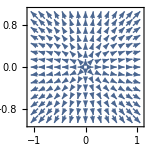

```mathematica
VectorPlot[
{x,y},{x,-1,1},{y,-1,1},
ImageSize->{150,150},FrameLabel->{x,y}
]
```

#### → 2. Tracé normalisé du champ de vecteurs de l’identité

Même tracé avec l’option VectorScale qui contrôle :
	la longueur,
	la taille de la pointe des flèches
	None ici en troisième position force tous les vecteurs à la même taille

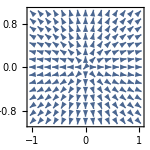

```mathematica
VectorPlot[
{x,y},{x,-1,1},{y,-1,1},
VectorScale->{Tiny,Automatic,None},
ImageSize->{150,150},FrameLabel->{x,y}
]
```

#### → 3. Idem + 1 ligne de flot

Même tracé avec l’option StreamPoints pour suivre le flot (ou les flèches) à partir du point {0.3,0.2}

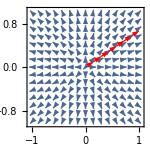

```mathematica
VectorPlot[
{x,y},{x,-1,1},{y,-1,1},
VectorScale->{Tiny,Automatic,None},
StreamPoints->{{{0.3,0.2}}},StreamStyle->{Red,Thick},
ImageSize->{150,150},FrameLabel->{x,y}
]
```

### → C. VectorPlot de Symétrie Orthogonale[λ, θ] dans un Manipulate

Champ de vecteurs d’une symétrie orthogonale d’angle θ, et d’homothétie de rapport λ

#### → 1. VectorPlot d’une application linéaire simple dans un Manipulate

D’un point de vue code (cf. cellule cachée), on remarque :
	l’utilisation très recommandée de la fonction With[], 
		parce qu’elle très efficace (deux fois plus rapide que Module[]), et 
		parce qu’elle oblige le programmeur à structurer et à documenter les ordres logiques d’évaluation.

Le code utilise les 2 options de VectorPlot[], VectorScale et StreamPoints vues précédemment. 
Il comporte d’autres éléments de code intéressants : :
	l’objet original Locator pour déplacer interactivement un objet dans un graphique,
	des aspects d’affichage un peu techniques comme Control[], ou Style[], faciles à comprendre.

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ------------------- *)
With[{a=λ Cos[θ],b=λ Sin[θ],c=λ Sin[θ],d=-λ Cos[θ]},
With[{mat=({{a, b}, {c, d}})},
(* II. -------Affichages ----------------------------------------- *)
VectorPlot[
{a*x+b*y,c*x+d*y},{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{250,250},FrameLabel->{x,y}
]
]],
(* III. ------Contrôles des variables du Manipulate----------------- *)
Style["Matrice de Symétrie Orthogonale[λ, θ] :",Bold],
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,0,"θ"},-π,π,.01,Appearance->"Labeled"}],
{{p,{.5,.5}},{-1,-1},{1,1},Locator}
]
```

#### → 2. Texte et VectorPlot dans deux colonnes adjacentes

Nous reprenons le code précédent en rajoutant au moyen de Eigensystem[] le calcul des valeurs propres, et des vecteurs propres de la matrice ainsi que de son déterminant au moyen de Det[].

Les changements de code servent principalement à présenter le texte et le VectorPlot dans deux colonnes au moyen :
	des fonctions Grid et Column d’organisation graphique en une colonne de texte et le graphique, et
	de la fonction TraditionalForm pour un bel affichage de texte.

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ----------------- *)
With[{a=λ Cos[θ],b=λ Sin[θ],c=λ Sin[θ],d=-λ Cos[θ]},
With[{dvec=({{x'}, {y'}}),vec=({{x}, {y}}),mat=({{a, b}, {c, d}})},
With[(* Valeurs propres et vecteurs propres de la matrice *)
{esys=Eigensystem[mat],det=Det[mat] },
With[{
λ1=esys⟦1,1⟧,λ2=esys⟦1,2⟧,
vec1=({{esys⟦2,1⟧⟦1⟧}, {esys⟦2,1⟧⟦2⟧}}),vec2=({{esys⟦2,2⟧⟦1⟧}, {esys⟦2,2⟧⟦2⟧}})
},
(* II. -------Affichages ------------------------------------ *)
Grid[{{
(* A. Texte de droite *)
Style[Text[Column[{
Text[TraditionalForm[Row[{"f : ℝ^2 ⟶ ℝ^2"}]]],
Text[TraditionalForm[Row[{"f :(x
y)↦(a | b
c | d)( x
 y)"}]]],
"",
Text[TraditionalForm[Row[{dvec , " = " , mat, vec}]]],
Text[TraditionalForm[Row[{" déterminant = ",det}]]],
"",
Text[TraditionalForm[Row[{"λ_1 = ",NumberForm[λ1,{5,2}]}]]],
Text[TraditionalForm[Row[{"λ_2 = ",NumberForm[λ2,{5,2}]}]]],
"",
Text[TraditionalForm[Row[{"ν_1 = ",NumberForm[vec1,{5,2}]}]]],
Text[TraditionalForm[Row[{"ν_2 = ",NumberForm[vec2,{5,2}]}]]],
"                                                      "
}]],12],
(* B. Figure de gauche *)
VectorPlot[
{a*x+b*y,c*x+d*y},{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{250,250},FrameLabel->{x,y}
]
}}]
]]]],
(* III. ------Contrôles des variables du Manipulate---------------- *)
Style["Matrice de Symétrie Orthogonale[λ, θ] :",Bold],
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,0,"θ"},-π,π,.01,Appearance->"Labeled"}],
{{p,{.5,.5}},{-1,-1},{1,1},Locator}
]
```

## → V. Expressions des Solutions d’EDO avec Mathematica

Nous allons aborder les aspects pratiques et techniques de résolution d’EDO avec Mathematica au travers de l’exemple de cinétique de Michaelis-Menten.

Une expression explicite, formelle ou symbolique de la solution d'un système d'équations différentielle est souvent préférable, mais souvent impossible.

Quand cela est possible, Mathematica est souvent capable de donner une solution sous forme symbolique. Sinon, il faut recourir à une solution numérique. Examinons les deux cas.

### → A. Résolution Formelle

#### → 1. Échec de résolution formelle d’EDO non linéaires

Pour obtenir la solution formelle d’une EDO avec Mathematica 11.0.1 il faudrait utiliser DSolve[].
Mais c’est inutile avec l’EDO ci-dessous, car il n'existe pas de solution sous une forme explicite de ces équations. Bizarrement avec la version 11.0.1, il faut plus de 12 minutes avant de s’en apercevoir....

```mathematica
DSolve[{
(* 2 EDO NON LINEAIRES avec 2 conditions initiales *)
s'[t]==-(k1*e0)*s[t]+(k1*s[t]+kr1)*c[t],
c'[t]==(k1*e0)*s[t]-(k1*s[t]+kr1+k2)*c[t],
s[0]==s0,
c[0]==0
},
{s[t], c[t]},t
]//Timing
```

{776.041,DSolve[{s'[t]==-e0 k1 s[t]+c[t] (kr1+k1 s[t]),c'[t]==e0 k1 s[t]-c[t] (k2+kr1+k1 s[t]),s[0]==s0,c[0]==0},{s[t],c[t]},t]}

Essais d'introduction des termes non linéaires : Reduce[] (version 11.0.1) et DSolve[] (versions 11.0.1, 7.0,5.2, 4.2) ne parviennent pas à donner une solution analytique (ce qui est attendu et normal).

```mathematica
Reduce[{
s'[t]==a3*s[t]*c[t],
c'[t]==-a3*s[t]*c[t],
s[0]==s0, c[0]==0
},
{s[t], c[t]},t,Reals
]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{s'[t]==a3 c[t] s[t],c'[t]==-a3 c[t] s[t],s[0]==s0,c[0]==0},{s[t],c[t]},t,Reals]

```mathematica
DSolve[{
s'[t]==a3*s[t]*c[t],
c'[t]==-a3*s[t]*c[t],
s[0]==s0, c[0]==0
},
{s[t], c[t]},t
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

Dans un premier temps, nous allons résoudre explicitement des équations plus simples en ne gardant que les termes linéaires. Remarque : on simplifie beaucoup la solution avec les conditions limites s[0]==s0, c[0]==0. 
→ 1. Résolution formelle d’EDO non linéaires (solution de l’exercice ici !)

a./ Résolution de l’équation différentielle (modèle logistique avec prélèvement)

```mathematica
solFormelle[a_,b_,c_,d_,t_]=Simplify[
x[t]/.DSolve[{
x'[t]==x[t](a-b x[t])-c,
x[0]==d
},x[t],t
]]⟦1⟧
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(a-√(-a^2+4 b c) Tan[1/2 √(-a^2+4 b c) t-ArcTan[(-a+2 b d)/(√(-a^2+4 b c))]])/(2 b)

Cette fonction peut contenir des parties complexes.

b./ Définir une fonction de  a, b, c, d, et t qui mémorise l’expression de la solution :

```mathematica
solFormelle[a,b,c,d,t]/.{a->1,b->0.02,c->0,d->0.01}
```

25. (1-(1.+0. ⅈ) Tanh[(4.2585+0. ⅈ)-(0.5+0. ⅈ) t])

Il est facile de s’en débarrasser avec la fonction Chop.

```mathematica
solFormelle[a,b,c,d,tt]/.{a->1,b->0.02,c->0,d->0.01}//Chop
```

25. (1-1. Tanh[4.2585-0.5 tt])

c./ Tracer la solution pour a=1, b=0.02, c=0, d=0.01, t=20

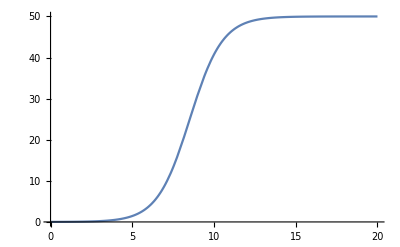

```mathematica
Plot[
solFormelle[a,b,c,d,t]/.{a->1,b->0.02,c->0,d->0.01},
{t,0,20},
PlotRange->{{0,20},All}
]
```

d./ Tracer la solution générale avec un Manipulate[] pour des valeurs raisonnables de  a, b, c, d et t :

```mathematica
Manipulate[
Plot[
solFormelle[a,b,c,d,t],
{t,0,tTot},
PlotRange->{{0,tTot},All}
],
{{a,1},0,10},
{{b,0.02},0,1},
{{c,0},0,2},
{{d,0.01},0,2},
{{tTot,20},0.001,100}
]
```

#### → 2. Résolution formelle d'EDO linéaires

Solution générale formelle d’un système linéaire : → 2. Résolution formelle d’EDO linéaires (solution ici !)

a./ Soit : A=(a | b
c | d), X=(x(t)
y(t))  et B=(b1
b2), résoudre le problème de Cauchy suivant :
	(ⅆ X)/(ⅆ t)=A X+B	∀t∈ℝ 
	X0=(x0
y0)  à t=0

```mathematica
solu=DSolve[{
x'[t]==a*x[t]+b*y[t],
y'[t]==c*x[t]+d*y[t],
x[0]==x0, y[0]==y0
},{x[t], y[t]},t
]//Simplify
```

{{x[t]→(ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t) (√(a^2+4 b c-2 a d+d^2) x0+√(a^2+4 b c-2 a d+d^2) ⅇ^(√(a^2+4 b c-2 a d+d^2) t) x0+a (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) x0-d (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) x0-2 b y0+2 b ⅇ^(√(a^2+4 b c-2 a d+d^2) t) y0))/(2 √(a^2+4 b c-2 a d+d^2)),y[t]→(ⅇ^(1/2 (a+d-√(a^2+4 b c-2 a d+d^2)) t) (2 c (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2) t)) x0+(a-a ⅇ^(√(a^2+4 b c-2 a d+d^2) t)+d (-1+ⅇ^(√(a^2+4 b c-2 a d+d^2) t))+√(a^2+4 b c-2 a d+d^2) (1+ⅇ^(√(a^2+4 b c-2 a d+d^2) t))) y0))/(2 √(a^2+4 b c-2 a d+d^2))}}

b./ Tracer la solution pour a=-1, b=2, c=3, d=-4, x0=1, y0=0, t alllant de 0 à 2.

```mathematica
{x[t], y[t]}/.solu/.{a->1,b->2,c->3,d->4,x0->1,y0->0}
```

{{(ⅇ^(1/2 (5-√33) t) (-1+√33+ⅇ^(√33 t)+√33 ⅇ^(√33 t)-4 (-1+ⅇ^(√33 t))))/(2 √33),√(3/11) ⅇ^(1/2 (5-√33) t) (-1+ⅇ^(√33 t))}}

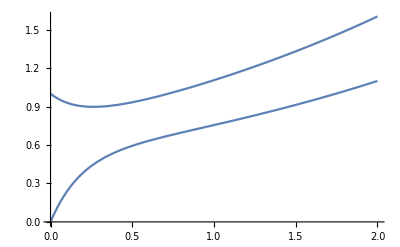

```mathematica
Plot[
{x[t], y[t]}/.solu/.{a->-1,b->2,c->3,d->-4,x0->1,y0->0},{t,0,2}
]
```

```mathematica
DSolve[{
s'[t]==-a1*s[t]+a2*c[t],
c'[t]==a1-b2*c[t],
s[0]==s0, c[0]==0
},{s[t], c[t]},t
]//Simplify
```

{{c[t]→(a1-a1 ⅇ^(-b2 t))/b2,s[t]→(-b2 ⅇ^(-a1 t) (a2 (-1+ⅇ^(a1 t))+b2 s0)+a1 (a2-a2 ⅇ^(-b2 t)+b2 ⅇ^(-a1 t) s0))/((a1-b2) b2)}}

Solution générale formelle d’un autre système linéaire dérivé :

```mathematica
DSolve[{
s'[t]==-a1*s[t]+a2*c[t],
c'[t]==a1*s[t]+b2*c[t],
s[0]==s0, c[0]==0
},{s[t], c[t]},t
]//Simplify
```

{{c[t]→(a1 ⅇ^(-1/2 (a1-b2+√(a1^2+4 a1 a2+2 a1 b2+b2^2)) t) (-1+ⅇ^(√(a1^2+4 a1 a2+2 a1 b2+b2^2) t)) s0)/(√(a1^2+b2^2+2 a1 (2 a2+b2))),s[t]→(ⅇ^(-1/2 (a1-b2+√(a1^2+4 a1 a2+2 a1 b2+b2^2)) t) (a1+b2-a1 ⅇ^(√(a1^2+4 a1 a2+2 a1 b2+b2^2) t)-b2 ⅇ^(√(a1^2+4 a1 a2+2 a1 b2+b2^2) t)+√(a1^2+4 a1 a2+2 a1 b2+b2^2) (1+ⅇ^(√(a1^2+4 a1 a2+2 a1 b2+b2^2) t))) s0)/(2 √(a1^2+b2^2+2 a1 (2 a2+b2)))}}

Champs de vecteurs ...

```mathematica
Manipulate[
VectorPlot[{
-a1*s+a2*c,
a1*s-b2*c
},
{s,-3,3},{c,-3,3},
VectorScale->{Tiny,Automatic,None},
ImageSize->Small
],
{{a1,1},0.1,10},
{{a2,3},0.1,10},
{{b2,1},0.1,10},SaveDefinitions->True
]
```

On peut aussi s’amuser à tracer des champs de vecteurs dans les cas non-linéaires, mais on peut choisir plusieurs modes de représentation. C’est simplement une façon de tracer les dérivées en fonction de s[t], et c[t] :
	s'[t]==-a1*s[t]+(a2*s[t])*c[t],
c'[t]==a1*s[t]-(b2*s[t])*c[t]

```mathematica
Manipulate[
VectorPlot[{
-a1*s+(a2*s)*c,
a1*s-(b2*s)*c
},
{s,-3,3},{c,-3,3},
VectorScale->{Tiny,Automatic,None},
ImageSize->Small
],
{{a1,1},0.1,10},
{{a2,1},0.1,10},
{{b2,1},0.1,10},SaveDefinitions->True
]
```

### B. Résolution numérique

Nous utiliserons les concentrations initiales :	e0=10^-3 mM, s0=1 mM

Nous allons d'abord résoudre le système d'équations différentielles pour : e_0/(K_m+s_0)<<1

On peut utiliser essentiellement 3 types de méthodes pour introduire les valeurs numériques dans  ces résolutions numériques :
1/ Programmation Procédurale (Déclarative ou Impérative),
2/ Programmation par Règles,
3/ Programmation Fonctionnelle.

#### 1. Programmation Procédurale (Déclarative ou Impérative) :

Il s'agit de mettre dans la mémoire le plus tôt possible les valeurs numériques indispensables aux calculs. Cette stratégie n'est pas mauvaise ici, puisqu'il s'agit d'une résolution numérique et que la fonction pourrait être compilée avec les valeurs mises en mémoire.

a./ mettre les valeurs numériques dans l’équation

Cette méthode est immédiate, rapide et directe, mais n’est pas très souple. Un inconvénient important est que les valeurs sont attribuées sans faire explicitement le lien avec des constantes symboliques.

```mathematica
solu=NDSolve[
{
s'[t]==-10*s[t]+(10000*s[t]+1000)*c[t],
c'[t]==10*s[t]-(10000*s[t]+2000)*c[t],
s[0]==1, c[0]==0
},
{s[t], c[t]},
{t,0,10^-3}]
```

{{s[t]→InterpolatingFunction[{{0., 0.001}}, <>][t],c[t]→InterpolatingFunction[{{0., 0.001}}, <>][t]}}

b./ définir des constantes et fixer leurs valeurs dès le départ

Cette méthode a l'avantage de fixer les valeurs dans la mémoire.
Mais cette méthode a aussi l'inconvénient de fixer les valeurs dans la mémoire.
Or, 95% des erreurs de programmation sont liées à des déclarations dans la mémoire : ce n'est donc pas une très bonne approche sauf si l'on ne veut résoudre qu'un seul problème (et encore !).

```mathematica
(k1=10^4; k2=10^3; kr1=10^3; e0=10^-3;s0=1 );
solu=NDSolve[
{
s'[t]==-(k1*e0)*s[t]+(k1*s[t]+kr1)*c[t],
c'[t]==(k1*e0)*s[t]-(k1*s[t]+kr1+k2)*c[t],
s[0]==s0, c[0]==0
},
{s[t], c[t]},
{t,0,10^-3}]
```

{{s[t]→InterpolatingFunction[{{0., 0.001}}, <>][t],c[t]→InterpolatingFunction[{{0., 0.001}}, <>][t]}}

#### 2/ Programmation par Règles :

Utiliser les règles de substitution, mais il faut alors la faire au moment où l'on pose les équations, car il n'est pas possible de procéder à l'intégration numérique à partir de valeurs symboliques !
Étant donnée la nature du calcul, l'idée est bien la même que précédemment. L'avantage dans cette approche est que les variables restent symboliques et qu'elles n'ont des valeurs numériques que localement.
On distingue donc bien le problème symbolique, et le problème numérique.

```mathematica
ClearAll[k1,k2,kr1,e0,s0]
solu=NDSolve[
{
s'[t]==-(k1*e0)*s[t]+(k1*s[t]+kr1)*c[t],
c'[t]==(k1*e0)*s[t]-(k1*s[t]+kr1+k2)*c[t],
s[0]==s0, c[0]==0
}/.{k1->10^4, k2->10^3, kr1->10^3, e0->10^-3,s0->1 },
{s[t], c[t]},
{t,0,10^-3}
]
```

{{s[t]→InterpolatingFunction[{{0., 0.001}}, <>][t],c[t]→InterpolatingFunction[{{0., 0.001}}, <>][t]}}

#### 3/ Programmation Fonctionnelle (À VALIDER)

Le problème est résolu à l'aide d'une seule fonction. C'est l'approche la plus mathématique qui combine les avantages de l'approche précédente et la clarté de l'approche procédurale. Il s'agit de poser les valeurs avant d'écrire les équations avec la fonction : With[définitions, expression à calculer].

Cette solution est bonne mais elle a l’inconvénient de cacher le symbole solu, à l’intérieur du With[].

```mathematica
With[{k1=10^4, k2=10^3, kr1=10^3, e0=10^-3, s0=1,tTot=10^-3},
solu=NDSolve[
{
s'[t]==-(k1*e0)*s[t]+(k1*s[t]+kr1)*c[t],
c'[t]==(k1*e0)*s[t]-(k1*s[t]+kr1+k2)*c[t],
s[0]==s0, c[0]==0
},
{s[t], c[t]},
{t,0,tTot}
];
]
```

```mathematica
solu
```

{{s[t]→InterpolatingFunction[{{0., 0.001}}, <>][t],c[t]→InterpolatingFunction[{{0., 0.001}}, <>][t]}}

Définition d’une fonction avec des valeurs par défaut :

```mathematica
soluFunc[k1_:10^4,k2_:10^3,kr1_:10^3,e0_:10^-3,s0_:1,tTot_:10^-3]:=NDSolve[
{
s'[t]==-(k1*e0)*s[t]+(k1*s[t]+kr1)*c[t],
c'[t]==(k1*e0)*s[t]-(k1*s[t]+kr1+k2)*c[t],
p'[t]==k2*c[t],
s[0]==s0, c[0]==0,  p[0]==0
},
{s[t], c[t],p[t]},
{t,0,tTot}
]
```

```mathematica
soluFunc[]==soluFunc[(*k1*)10^4,(*k2*)10^3,(*kr1*)10^3,(*e0*)10^-3,(*s0*)1,(*tTot*)10^-3];
```

#### 4/ La variable globale "solu"

Dans chacun des cas ci-dessus, en réalité, on récupère la solution à l'aide de la variable globale "solu" qui est une fonction numérique d’interpolation.

solu est définie à l’extérieur de la fonction dans les 2 premiers cas, et dans la fonction dans le 3ième cas, mais c’est dans tous les cas une variable globale. Pour que solu soit une variable locale, il aurait fallu la mettre dans les définitions entre {} d’un With[]. Mais alors nous n’y aurions pas eu accès.

Dans tous les cas, solu est une fonction numérique de la variable implicite ou du symbole global t.

## VI. Résolution pratique d’EDO numériques

### A. Résolution du système d'EDO pour e_0/(K_m+s_0)<<1

On utilise soluFunc[] pour définir les équations de type Michaelis-Menten avec les constantes de vitesse suivantes : 
	k1=10^4  en mM^-1 s^-1; k2=10^3 s^-1,kr1=10^3 s^-1
et les concentrations initiales :	e0=10^-3 mM, s0=1 mM (excès de substrat). On a alors : 
	K_M=(kr1+k2)/k1=(10^3+10^3)/10^4=0.2 mM

#### 1/ Evaluate : Tracés de la solution (temps court)

On peut tracer les trajectoires solution en faisant, pour S[t]. Attention : il n’est toutefois pas possible de tracer la solution en faisant :

```mathematica
Plot[(s[t]/.soluFunc[]),{t,0,1/10^3},
AxesLabel->{t,S[t]},PlotRange->All
]
```

NDSolve::dsvar: 2.04286×10^-8 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{s'[2.04286×10^-8]==-10 s[2.04286×10^-8]+c[2.04286×10^-8] (1000+Times[«2»]),c'[2.04286×10^-8]==10 s[2.04286×10^-8]-c[2.04286×10^-8] (2000+Times[«2»]),p'[2.04286×10^-8]==1000 c[2.04286×10^-8],s[0]==1,c[0]==0,p[0]==0},{«1»},{2.04286×10^-8,0,1/1000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 2.04286×10^-8 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{s'[2.04286×10^-8]==-10. s[2.04286×10^-8]+c[2.04286×10^-8] (1000.+Times[«2»]),c'[2.04286×10^-8]==10. s[2.04286×10^-8]-1. c[2.04286×10^-8] (2000.+Times[«2»]),p'[2.04286×10^-8]==1000. c[2.04286×10^-8],s[0.]==1.,c[0.]==0.,p[0.]==0.},{«1»},{2.04286×10^-8,0.,0.001}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{s'[0.0000204286]==-10 s[0.0000204286]+c[0.0000204286] (1000+Times[«2»]),c'[0.0000204286]==10 s[0.0000204286]-c[0.0000204286] (2000+Times[«2»]),p'[0.0000204286]==1000 c[0.0000204286],s[0]==1,c[0]==0,p[0]==0},{«1»},{0.0000204286,0,1/1000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

Mathematica ne peut logiquement pas intégrer cette équation ET la tracer en même temps.

En effet, le même symbole t est utilisé à la fois :
	pour effectuer l’intégration du système d’EDO, et 
	pour tenter de faire le tracé.
Il y a deux moyens simples d’éviter ce conflit de symboles.

Le premier moyen consiste à récupérer la solution en fonction de t : (s[t]/.solu[]), puis à remplacer t dans la solution numérique interpolée par tt. On trace ensuite cette solution numérique en fonction de tt.

```mathematica
Plot[
(s[t]/.soluFunc[])/.t->tt,{tt,0,1/10^3},
AxesLabel->{t,S[t]},PlotRange->All,ImageSize->130
]
```

-Graphics-

Le moyen recommandé plus simple et plus élégant consiste à utiliser la fonction Evaluate[], qui hiérarchise et dissocie le calcul de la solution numérique et le tracé des solutions :

```mathematica
Plot[
Evaluate[s[t]/.soluFunc[]],{t,0,1/10^3},
AxesLabel->{t,S[t]},PlotRange->All,ImageSize->130
]
```

-Graphics-

```mathematica
Plot[
Evaluate[{c[t],p[t]}/.soluFunc[]],{t,0,1/10^3},
AxesLabel->{"t","C[t],P[t]"},PlotRange->All,
PlotLegends->{"C[t]","P[t]"},ImageSize->130
]
```

-Graphics-

On observe ci-dessus l'établissement dans la première phase, puis le maintien du régime stationnaire à l'échelle de temps très court.

#### 2/ Tracés de la solution (temps long 2 secondes = 2000 ms)

Recalculons et mémorisons la solution pour un temps long :

```mathematica
ClearAll[solu]
solu=soluFunc[(*k1*)10^4,(*k2*)10^3,(*kr1*)10^3,(*e0*)10^-3,(*s0*)1,(*tTot*)2]
```

NDSolve::ndode: The equations {0.18[0]==0} are not differential equations or initial conditions in the dependent variables {p,s}.

NDSolve[{s'[t]==-10 s[t]+0.18[t] (1000+10000 s[t]),0==10 s[t]-0.18[t] (2000+10000 s[t]),p'[t]==1000 0.18[t],s[0]==1,0.18[0]==0,p[0]==0},{s[t],0.18[t],p[t]},{t,0,2}]

Traçons les évolutions des concentrations en fonction du temps :

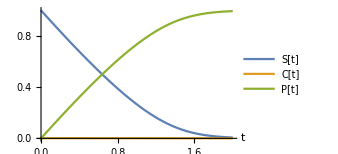

```mathematica
Plot[Evaluate[{s[t],c[t],p[t]}/.solu],{t,0,2000/10^3},
AxesLabel->{"t"},PlotRange->All,
PlotLegends->{"S[t]","C[t]","P[t]"},ImageSize->250]
```

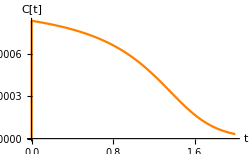

```mathematica
Plot[Evaluate[{c[t]}/.solu],{t,0,2000/10^3},PlotStyle->Orange,
AxesLabel->{"t","C[t]"},PlotRange->All,ImageSize->250]
```

A l'échelle de temps long, on observe ci-dessus la consommation du substrat qui tend vers 0, alors que la formation de produit tend vers 1. L'hypothèse de l'état stationnaire pour le complexe enzyme.substrat n'est admissible que lors de la première phase de la cinétique (la première seconde sans le tout début), comme on peut le voir sur le deuxième graphe.

#### 3/ Superposition de graphiques avec Show

Dans l'exemple ci-dessous, on superpose les graphiques gS, gC et gP calculés séparément. Il est ensuite très facile de les tracer ensemble avec Show[{gS,gC,gP}] et les options graphiques voulues.

```mathematica
gS=Plot[Evaluate[s[t]/.solu],{t,0,2000/10^3},PlotStyle->Blue];
```

```mathematica
gC=Plot[Evaluate[c[t]/.solu],{t,0,2000/10^3},PlotStyle->Orange];
```

```mathematica
gP=Plot[Evaluate[p[t]/.solu],{t,0,2000/10^3},PlotStyle->Darker[Green]];
```

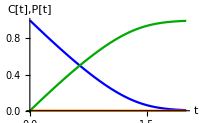

```mathematica
Show[{gS,gC,gP},
AxesLabel->{"t","C[t],P[t]"},
PlotRange->All,ImageSize->200
]
```

Ce type de calcul peut être très intéressant dans le cas de nombreux graphiques et de calculs longs par exemples.

### B. Résolution du système d'EDO pour e_0/(K_m+s_0)≈1

On utilise soluFunc[] pour définir les équations de type Michaelis-Menten avec les mêmes constantes de vitesse et les concentrations initiales :	e0=1mM, s0=1 mM (épuisement du substrat).

#### 1/ Jolis tracés de la solution

Recalculons et mémorisons la solution pour ce nouveau cas :

```mathematica
solu=soluFunc[(*k1*)10^4,(*k2*)10^3,(*kr1*)10^3,(*e0*)1,(*s0*)1,(*tTot*)10^-3]
```

{{s[t]→InterpolatingFunction[{{0., 0.001}}, <>][t],c[t]→InterpolatingFunction[{{0., 0.001}}, <>][t],p[t]→InterpolatingFunction[{{0., 0.001}}, <>][t]}}

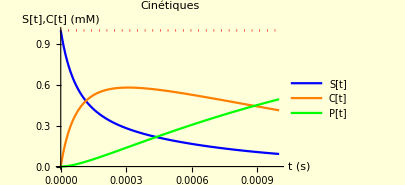

```mathematica
Plot[
Evaluate[{s[t],c[t],p[t],1}/.solu,{t,0,10^-3}],
PlotRange->All,PlotStyle->{Blue,Orange,Green,{Dotted,Red}},
PlotLegends->{"S[t]","C[t]","P[t]"},
AxesLabel->{"t (s)","S[t],C[t] (mM)"},BaseStyle->{FontFamily->"Times",FontSize->12,FontColor->Black},
Background->Lighter[Yellow,0.85],
PlotLabel->"Cinétiques",ImageSize->300
]
```

#### 2/ Diagrammes de phase en 2D ou 3D

Il est facile de tracer un diagramme de phase en 2D avec ParametricPlot[] à partir des solutions calculées :

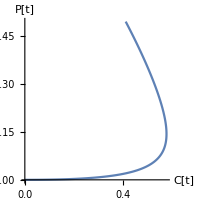

```mathematica
ParametricPlot[
Evaluate[{c[t],p[t]}/.solu],
{t,0,10^-3},
AxesLabel->{"C[t]","P[t]"},PlotRange->All,ImageSize->200
]
```

Il est facile de tracer un diagramme de phase en 3D avec ParametricPlot3D[] à partir des solutions calculées :

```mathematica
ParametricPlot3D[
Evaluate[{s[t],c[t],p[t]}/.solu],
{t,0,10^-3},
AxesLabel->{"C[t]","P[t]"},PlotRange->All,ImageSize->200
]
```

-Graphics3D-

#### 3/ Manipulate interactif des solutions (cas général)

Si soluFunc[] est validé, on dispose d’un joli Manipulate efficace et très interactif :

```mathematica
ClearAll[a,b,c,d]
Manipulate[
With[{(* Calcul préliminaire de la solution numérique *)
solu=soluFunc[k1(*10^4*),k2(*10^3*),kr1(*10^3*),e0(*1*),s0(*1*),tTot(*10^-3*)]
},
Plot[(* Tracés *)
Evaluate[{s[t],c[t],p[t](*,1*)}/.solu],{t,0,tTot},
PlotRange->All,PlotStyle->{Blue,Orange,Green(*,{Dotted,Red}*)},
PlotLegends->{"S[t]","C[t]","P[t]"},
(*AxesLabel->{"t (s)","S[t],C[t] (mM)"}, Inutile si Frame->True *)BaseStyle->{FontFamily->"Times",FontSize->12,FontColor->Black},
Background->Lighter[Yellow,0.85],
PlotLabel->"Cinétiques",Frame->True,ImageSize->350
]],
{{k1,1.5*10^3},10,10^5},
{{k2,0.2*10^3},10,10^4},
{{kr1,0.01*10^3},10,10^4},
{{e0 (*mM*),0.25},10^-3,1},
{{s0 (*mM*),1},0.1,10},
{{tTot (*s*),30*10^-3},10^-5,10},SaveDefinitions->True
]
```

## Exercices EDO

## → I. Elaboration d’un Manipulate pour EDO

### → A. VectorPlot de 9 applications linéaires fonctions de λ et/ou θ

Champ de vecteurs 9 applications linéaires fondamentales d’angle θ, et/ou d’homothétie H[λ] de rapport λ

#### → 1. Manipulate pour afficher une matrice parmi 9

En utilisant les définitions de matrices ci-dessous, écrivons un Manipulate pour afficher l’une de ces matrices au choix ainsi que le premier coefficient de la matrice :

```mathematica
(* -------Définition de 9 matrices 2D ---------------------------- *)
(* Identite H[λ] *)                 matIdλ[λ_,θ_]:=({{λ, 0}, {0, λ}})
(* SymetrieCentrale H[λ]*) matSymCentλ[λ_,θ_]:=({{-λ, 0}, {0, -λ}})
(* Symetrie/X H[λ] *)             matSymXλ[λ_,θ_]:=({{λ, 0}, {0, -λ}})
(* Symetrie/Y H[λ] *)             matSymYλ[λ_,θ_]:=({{-λ, 0}, {0, λ}})
(* Symetrie/Y=X H[λ] *)        matSymYeqXλ[λ_,θ_]:=({{0, λ}, {λ, 0}})
(* SymetrieOrthogonale/axe[θ] H[λ] *) matSymλθ[λ_,θ_]:=({{λ Cos[θ], λ Sin[θ]}, {λ Sin[θ], -λ Cos[θ]}})
(* Rotation[θ] H[λ] *)           matRotλθ[λ_,θ_]:=({{λ Cos[θ], -λ Sin[θ]}, {λ Sin[θ], λ Cos[θ]}})
(* Projection[θ] H[λ] *) matProjλθ[λ_,θ_]:=({{λ Cos[θ]^2, λ Sin[θ]Cos[θ]}, {λ Sin[θ]Cos[θ], λ Sin[θ]^2}})
(* Cisaillement[λ] *)             matCisλ[λ_,θ_]:=({{1, λ}, {0, 1}}) 
(* ---------------------------------------------------------------- *)
```

```mathematica
(* Manipulate : choix d'une matrice, et affichage du 1er coeff *)
Manipulate[
{mat[λ,θ]//MatrixForm,mat[λ,θ]⟦1,1⟧},
{
{mat,matIdλ},
{matIdλ,matSymCentλ,matSymXλ,matSymYλ,matSymYeqXλ,matSymλθ,matRotλθ,matProjλθ,matCisλ}},SaveDefinitions->True
]
```

#### → 2. Manipulate pour tracer le champ de vecteurs d’une matrice parmi 9

Avec le code vu en préambule, on obtient le Manipulate pour tracer le champ de vecteurs d’une matrice parmi 9 :

```mathematica
Manipulate[
VectorPlot[
{mat[λ,θ]⟦1,1⟧ x+ mat[λ,θ]⟦1,2⟧ y, mat[λ,θ]⟦2,1⟧ x+mat[λ,θ]⟦2,2⟧ y},
{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},
VectorScale->{Tiny,Automatic,None},
ImageSize->{250,250},FrameLabel->{x,y}
],
Style["Choix de Matrices particulières ",Bold],
{{mat,matIdλ},{matIdλ,matSymCentλ,matSymXλ,matSymYλ,matSymYeqXλ,matSymλθ,matRotλθ,matProjλθ,matCisλ}},
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,0,"θ"},-π,π,.01,Appearance->"Labeled"}],
(* Point P des Initialisations de la ligne du champ de vecteurs *)
{{p,{.5,.5}},{-1,-1},{1,1},Locator},SaveDefinitions->True
]
```

#### → 3. Idem avec Texte et VectorPlot dans deux colonnes adjacentes

Avec le code vu en préambule, on obtient le Manipulate plus complet dont vous étudierez le code et les effets.

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ------------------- *)
With[{dvec=({{x'}, {y'}}),vec=({{x}, {y}})},
With[(* Calcul des valeurs propres et des vecteurs propres de la matrice *)
{esys=Eigensystem[mat[λ,θ]],det=Det[mat[λ,θ]] },
With[{λ1=esys⟦1,1⟧,λ2=esys⟦1,2⟧,
vec1=({{esys⟦2,1⟧⟦1⟧}, {esys⟦2,1⟧⟦2⟧}}),vec2=({{esys⟦2,2⟧⟦1⟧}, {esys⟦2,2⟧⟦2⟧}})
},
(* II. -------Affichages ---------------------------------------- *)
Grid[{{
(* A. Texte de droite *)
Style[Text[Column[{
Text[TraditionalForm[Row[{"f : ℝ^2 ⟶ ℝ^2"}]]],
Text[TraditionalForm[Row[{"f :(x
y)↦(a | b
c | d)( x
 y)"}]]],
"",
Text[TraditionalForm[Row[{dvec , " = " ,  mat[λ,θ], vec}]]],
Text[TraditionalForm[Row[{" déterminant = ",det}]]],
"",
Text[TraditionalForm[Row[{"λ_1 = ",NumberForm[λ1,{5,2}]}]]],
Text[TraditionalForm[Row[{"λ_2 = ",NumberForm[λ2,{5,2}]}]]],
"",
Text[TraditionalForm[Row[{"ν_1 = ",NumberForm[vec1,{5,2}]}]]],
Text[TraditionalForm[Row[{"ν_2 = ",NumberForm[vec2,{5,2}]}]]],
"                                                      "
}]],12],
(* B. Figure de gauche *)
VectorPlot[
{mat[λ,θ]⟦1,1⟧ x+ mat[λ,θ]⟦1,2⟧ y, mat[λ,θ]⟦2,1⟧ x+mat[λ,θ]⟦2,2⟧ y},{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{300,300},FrameLabel->{x,y}
]
}}]
]]],
(* III. ------Contrôles des variables du Manipulate---------------- *)
Style["Choix de Matrices particulières fonction de λ et θ ",Bold],
{{mat,matSymλθ},{matIdλ,matSymCentλ,matSymXλ,matSymYλ,matSymYeqXλ,matSymλθ,matRotλθ,matProjλθ,matCisλ}},
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,π/3,"θ"},-π,π,.01,Appearance->"Labeled"}],
(* Point P des Initialisations de la ligne du champ de vecteurs *)
{{p,{.5,.5}},{-1,-1},{1,1},Locator}
]
```

#### → 4. Idem + matrice générale + Axes de symétrie et vecteurs propres

On rajoute la possibilité de traiter une matrice réelle générale en activant le “generalFlag”, et en contrôlant les valeurs des coefficients a, b, c, d de cette matrice.

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ------------------- *)
With[{dvec=({{x'}, {y'}}),vec=({{x}, {y}}), matCalc=If[generalFlag,({{a, b}, {c, d}}),mat[λ,θ]]},
With[(* Valeurs propres et vecteurs propres de la matrice *)
{esys=Eigensystem[matCalc],det=Det[matCalc] },
With[{λ1=esys⟦1,1⟧,λ2=esys⟦1,2⟧,
vec1=({{esys⟦2,1⟧⟦1⟧}, {esys⟦2,1⟧⟦2⟧}}),vec2=({{esys⟦2,2⟧⟦1⟧}, {esys⟦2,2⟧⟦2⟧}})
},
(* II. -------Affichages --------------------------------------- *)
Grid[{{
(* A. Texte de droite *)
Style[Text[Column[{
Text[TraditionalForm[Row[{"f : ℝ^2 ⟶ ℝ^2"}]]],
Text[TraditionalForm[Row[{"f :(x
y)↦(a | b
c | d)( x
 y)"}]]],
"",
Text[TraditionalForm[Row[{dvec , " = " ,  matCalc, vec}]]],
Text[TraditionalForm[Row[{" déterminant = ",det}]]],
"",
Text[TraditionalForm[Row[{"λ_1 = ",NumberForm[λ1,{5,2}]}]]],
Text[TraditionalForm[Row[{"λ_2 = ",NumberForm[λ2,{5,2}]}]]],
"",
Text[TraditionalForm[Row[{"ν_1 = ",NumberForm[vec1,{5,2}]}]]],
Text[TraditionalForm[Row[{"ν_2 = ",NumberForm[vec2,{5,2}]}]]],
"                                                      "
}]],12],
(* B. Figure de gauche *)
Show[
(* Champ de vecteurs *)
VectorPlot[
{matCalc⟦1,1⟧ x+ matCalc⟦1,2⟧ y, matCalc⟦2,1⟧ x+matCalc⟦2,2⟧ y},
{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{300,300},FrameLabel->{x,y}
],
(* Axes des vecteurs propres réels *)
Graphics[{
Thick,Orange,
Map[
Line[{-100#,100#}]&,
Select[Eigenvectors[matCalc],(Im[#⟦1⟧]==0&&Im[#⟦2⟧]==0)&]
]
}]
](* Fin de Show *)
}}](* Fin de Grid *)
]]](* Fin des With *),
(* III. ------Contrôles des variables du Manipulate---------------- *)
(* A. Liste des choix de matrices *)
Style["Choix de Matrices particulières fonction de λ et θ ",Bold],
{{mat,matSymλθ},{matIdλ,matSymCentλ,matSymXλ,matSymYλ,matSymYeqXλ,matSymλθ,matRotλθ,matProjλθ,matCisλ}},
(* B. Contrôles des paramètres numériques *)
(* Matrices particulières fonction de λ ou θ *)
Row[{
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,π/3,"θ"},-π,π,.01,Appearance->"Labeled"}]
}],
(* Point P des Initialisations de la ligne du champ de vecteurs *)
{{p,{.5,.5}},{-1,-1},{1,1},Locator},
(* Matrices "General[a,b,c,d]" avec initialisation Romeo et Juliette *)
{{generalFlag,False},{True,False}},
Style["Matrices générales fonction de a, b, c, d ",Bold],
Row[{
Control[{{a,.5,"a"},-1,1,.01,Appearance->"Labeled"}],
Control[{{b,-.75,"b"},-1,1,.01,Appearance->"Labeled"}]
}],
Row[{
Control[{{c,.1,"c"},-1,1,.01,Appearance->"Labeled"}],
Control[{{d,.5,"d"},-1,1,.01,Appearance->"Labeled"}]
}]
]
```

### → B. VectorPlot de 10 applications linéaires + solutions EDO

#### → 1. Idem + calcul et affichage des solutions EDO

On rajoute :
	la partie calcul des EDO à la fin de I. Définitions et calcul des variables, et 
	le tracé des solutions à la fin de II. Affichage,
	le contrôle du temps total de calcul de l’EDO à la fin du III. Contrôles des variables du Manipulate.

La solution de l’EDO est tracée en pointillés noirs à partir du point P donné par le “Locator”.

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ------------------- *)
With[{dvec=({{x'}, {y'}}),vec=({{x}, {y}}), matCalc=If[generalFlag,({{a, b}, {c, d}}),mat[λ,θ]]},
With[(* Valeurs propres et vecteurs propres de la matrice *)
{esys=Eigensystem[matCalc],det=Det[matCalc] },
With[{λ1=esys⟦1,1⟧,λ2=esys⟦1,2⟧,
vec1=({{esys⟦2,1⟧⟦1⟧}, {esys⟦2,1⟧⟦2⟧}}),vec2=({{esys⟦2,2⟧⟦1⟧}, {esys⟦2,2⟧⟦2⟧}})
},
With[(* Solution EDO de R[t] et J[t] initialisées avec P Locator *)
{solu = NDSolve[{
R'[t] == matCalc⟦1,1⟧ R[t]+ matCalc⟦1,2⟧  J[t],
J'[t] == matCalc⟦2,1⟧  R[t]+ matCalc⟦2,2⟧  J[t],
R[0]==p⟦1⟧, J[0]==p⟦2⟧}, {R[t], J[t]}, {t, 0, T},
 PrecisionGoal -> 3
] },
(* II. -------Affichages --------------------------------------- *)
Grid[{{
(* A. Texte de droite *)
Style[Text[Column[{
Text[TraditionalForm[Row[{"f : ℝ^2 ⟶ ℝ^2"}]]],
Text[TraditionalForm[Row[{"f :(x
y)↦(a | b
c | d)( x
 y)"}]]],
"",
Text[TraditionalForm[Row[{dvec , " = " ,  matCalc, vec}]]],
Text[TraditionalForm[Row[{" déterminant = ",det}]]],
"",
Text[TraditionalForm[Row[{"λ_1 = ",NumberForm[λ1,{5,2}]}]]],
Text[TraditionalForm[Row[{"λ_2 = ",NumberForm[λ2,{5,2}]}]]],
"",
Text[TraditionalForm[Row[{"ν_1 = ",NumberForm[vec1,{5,2}]}]]],
Text[TraditionalForm[Row[{"ν_2 = ",NumberForm[vec2,{5,2}]}]]],
"                                                      "
}]],12],
(* B. Figure de gauche *)
Show[
(* Champ de vecteurs *)
VectorPlot[
{matCalc⟦1,1⟧ x+ matCalc⟦1,2⟧ y, matCalc⟦2,1⟧ x+matCalc⟦2,2⟧ y},
{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{300,300},FrameLabel->{x,y}
],
(* Axes des vecteurs propres réels *)
Graphics[{
Thick,Orange,
Map[
Line[{-100#,100#}]&,
Select[Eigenvectors[matCalc],(Im[#⟦1⟧]==0&&Im[#⟦2⟧]==0)&]
]
}],
(* Tracé de la solution de l'équation différentielle *)
ParametricPlot[
Evaluate[{R[t],J[t]}/.solu⟦1⟧ ], {t, 0, T},
PlotRange -> All,PlotStyle -> {Black, Dashed},
AspectRatio -> 1,
MaxRecursion -> ControlActive[Automatic, 8]
]
](* Fin de Show *)
}}](* Fin de Grid *)
]]]](* Fin des With *),
(* III. ------Contrôles des variables du Manipulate---------------- *)
(* A. Liste des choix de matrices *)
Style["Choix de Matrices particulières fonction de λ et θ ",Bold],
{{mat,matIdλ},{matIdλ,matSymCentλ,matSymXλ,matSymYλ,matSymYeqXλ,matSymλθ,matRotλθ,matProjλθ,matCisλ}},
(* B. Contrôles des paramètres numériques *)
(* Matrices particulières fonction de λ ou θ *)
Row[{
Control[{{λ,1,"λ"},-5,5,.01,Appearance->"Labeled"}],
Control[{{θ,0,"θ"},-π,π,.01,Appearance->"Labeled"}]
}],
(* Point P des Initialisations de la ligne du champ de vecteurs *)
{{p,{.5,.5}},{-1,-1},{1,1},Locator},
(* Matrice generale[a,b,c,d]" avec initialisation Romeo et Juliette *)
{{generalFlag,False},{True,False}},
Style["Matrices générales fonction de a, b, c, d ",Bold],
Row[{
Control[{{a,.5,"a"},-1,1,.01,Appearance->"Labeled"}],
Control[{{b,-.75,"b"},-1,1,.01,Appearance->"Labeled"}]
}],
Row[{
Control[{{c,.1,"c"},-1,1,.01,Appearance->"Labeled"}],
Control[{{d,.5,"d"},-1,1,.01,Appearance->"Labeled"}]
}],
(* Equations différentielles *)
Control[{{T,10.0,"temps d'intégration"},0.1,20.0,.1,Appearance->"Labeled"}]
]
```

### → C. VectorPlot de 10 (applications + EDO) linéaires + cas non linéaire

#### 1. Redéfinition des matrices sans homothétie (À VALIDER)

L’homothétie de rapport λ complique beaucoup les calculs, alors qu’elle n’a pas d’effet dans VectorPlot qui remet à l’échelle. On introduit donc d’abord la simplification des matrices ci-dessous.
Dans le code du Manipulate, il suffit de changer une fois mat[λ,θ] en mat[θ] dans le code ci-dessous, et de modifier le contrôle des matrices avec les noms sans λ, mais avec seulement θ.

```mathematica
(* -------Liste de choix de 9 matrices 2D pour Manipulate --------- *)
(* Simplification en supprimant H[λ] l'homothétie de rapport λ *)
(* Identite *)                                         matId[ϕ_]:=({{1, 0}, {0, 1}})
(* SymetrieCentrale *)                       matSymCent[ϕ_]:=({{-1, 0}, {0, -1}})
(* Symetrie/X *)                                     matSymX[ϕ_]:=({{1, 0}, {0, -1}})
(* Symetrie/Y *)                                     matSymY[ϕ_]:=({{-1, 0}, {0, 1}})
(* Symetrie/Y=X *)                                 matSymYeqX[θ_]:=({{0, 1}, {1, 0}})
(* SymetrieOrthogonale/axe[θ] *) matSymθ[θ_]:=({{Cos[θ], Sin[θ]}, {Sin[θ], -Cos[θ]}})
(* Rotation[ϕ] *)                                   matRotθ[θ_]:=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}})
(* Projection[ϕ] *)  matProjθ[θ_]:=({{Cos[θ]^2, Sin[θ]Cos[θ]}, {Sin[θ]Cos[θ], Sin[θ]^2}})
(* Cisaillement[ϕ] *)                          matCisθ[θ_]:=({{1, θ}, {0, 1}}) 
(* ---------------------------------------------------------------- *)
```

#### → 2. Ajout d’un cas EDO non linéaire (Roméo et Juliette)

Puis on introduit la la possibilité de termes non linéaires dans la matrice, et dans l’EDO. Pour cela, il faut procéder aux modifications suivantes.

Dans  I. Définitions et calcul des variables, il faut :
	* remplacer la matrice(a | b 
c  | d) par
	 (a | b If[includeNonlinearTerms,JM-Abs[y] , 1]
c If[includeNonlinearTerms,RM-Abs[x] , 1]  | d)
	** remplacer mat[λ,θ] par mat[θ]
	*** faire les substitutions /.{Abs[y]→ Abs[J[t]] et /.{Abs[x]→ Abs[R[t]] dans les EDO.

À la fin du III. Contrôles des variables du Manipulate, il suffit de :
	supprimer le contrôle de λ, et
	d’ajouter le contrôle des coefficients non linéaires portant sur JM et RM de l’EDO .

```mathematica
Manipulate[
(* I. -------Definitions et calcul des variables ------------------- *)
With[{dvec=({{x'}, {y'}}),vec=({{x}, {y}}), 
(* On rajoute éventuellement les termes non linéaires de l'EDO de Roméo et Juliette *)
matCalc=If[generalFlag,
({{a, b If[includeNonlinearTerms,JM-Abs[y] , 1]}, {c If[includeNonlinearTerms,RM-Abs[x] , 1], d}}),
mat[θ]]
},
With[(* Valeurs propres et vecteurs propres de la matrice *)
{esys=Eigensystem[matCalc],det=Det[matCalc] },
With[{λ1=esys⟦1,1⟧,λ2=esys⟦1,2⟧,
vec1=({{esys⟦2,1⟧⟦1⟧}, {esys⟦2,1⟧⟦2⟧}}),vec2=({{esys⟦2,2⟧⟦1⟧}, {esys⟦2,2⟧⟦2⟧}})
},
With[(* Solution EDO de R[t] et J[t] initialisées avec P Locator *)
{solu = NDSolve[{
R'[t] ==  matCalc⟦1,1⟧ R[t]+( matCalc⟦1,2⟧ J[t]/.{Abs[y]-> Abs[J[t]]}),
J'[t] == (matCalc⟦2,1⟧ R[t]/.{Abs[x]-> Abs[R[t]]})+  matCalc⟦2,2⟧ J[t],
R[0]==p⟦1⟧, J[0]==p⟦2⟧}, {R[t], J[t]}, {t, 0, T},
 PrecisionGoal -> 3
]//Quiet(* Supprime messages : NDSolve : equations stiff *)
},
(* II. -------Affichages --------------------------------------- *)
Grid[{{
(* A. Texte de droite *)
Style[Text[Column[{
Text[TraditionalForm[Row[{"f : ℝ^2 ⟶ ℝ^2"}]]],
Text[TraditionalForm[Row[{"f :(x
y)↦(a | b
c | d)( x
 y)"}]]],
"",
Text[TraditionalForm[Row[{dvec , " = " ,  matCalc, vec}]]],
Text[TraditionalForm[Row[{" déterminant = ",det}]]],
"",
Text[TraditionalForm[Row[{"λ_1 = ",NumberForm[λ1,{5,2}]}]]],
Text[TraditionalForm[Row[{"λ_2 = ",NumberForm[λ2,{5,2}]}]]],
"",
Text[TraditionalForm[Row[{"ν_1 = ",NumberForm[vec1,{5,2}]}]]],
Text[TraditionalForm[Row[{"ν_2 = ",NumberForm[vec2,{5,2}]}]]],
"                                                      "
}]],12],
(* B. Figure de gauche *)
Show[
(* Champ de vecteurs *)
VectorPlot[
{matCalc⟦1,1⟧ x+ matCalc⟦1,2⟧ y, matCalc⟦2,1⟧ x+matCalc⟦2,2⟧ y},
{x,-1,1},{y,-1,1},
StreamPoints->{{p⟦1⟧,p⟦2⟧}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
ImageSize->{300,300},FrameLabel->{x,y}
],
(* Axes des vecteurs propres réels *)
Graphics[{
Thick,Orange,
Map[
Line[{-100#,100#}]&,
Select[Eigenvectors[matCalc],(Im[#⟦1⟧]==0&&Im[#⟦2⟧]==0)&]
]
}],
(* Tracé de la solution de l'équation différentielle *)
ParametricPlot[
Evaluate[{R[t],J[t]}/.solu⟦1⟧ ], {t, 0, T},
PlotRange -> All,PlotStyle -> {Black, Dashed},
AspectRatio -> 1,
MaxRecursion -> ControlActive[Automatic, 8]
]
](* Fin de Show *)
}}](* Fin de Grid *)
]]]](* Fin des With *),
(* III. ------Contrôles des variables du Manipulate---------------- *)
(* A. Liste des choix de matrices *)
Style["Choix de Matrices particulières fonction de λ et θ ",Bold],
{{mat,matId},{matId,matSymCent,matSymX,matSymY,matSymYeqX,matSymθ,matRotθ,matProjθ,matCisθ}},
(* B. Contrôles des paramètres numériques *)
(* Matrices particulières fonction de λ ou θ *)
Control[{{θ,0,"θ"},-π,π,.01,Appearance->"Labeled"}],
(* Point P des Initialisations de la ligne du champ de vecteurs *)
{{p,{.5,.5}},{-1,-1},{1,1},Locator},
(* Matrice generale[a,b,c,d]" avec initialisation Romeo et Juliette *)
{{generalFlag,False},{True,False}},
Style["Matrices générales fonction de a, b, c, d ",Bold],
Row[{
Control[{{a,.5,"a"},-1,1,.01,Appearance->"Labeled"}],
Control[{{b,-.75,"b"},-1,1,.01,Appearance->"Labeled"}]
}],
Row[{
Control[{{c,.1,"c"},-1,1,.01,Appearance->"Labeled"}],
Control[{{d,.5,"d"},-1,1,.01,Appearance->"Labeled"}]
}],
(* Equations différentielles *)
Control[{{T,10.0,"temps d'intégration"},0.1,20.0,.1,Appearance->"Labeled"}],
Delimiter,
"include negative effect of too much love (non linéarité) :  ",{{includeNonlinearTerms, False, ""}, {True, False}},
Row[{
Dynamic[Style[ "Juliet's love for Romeo\nbecomes counterproductive.", If[includeNonlinearTerms, Blue, Lighter[Gray]]]],
Control[{{JM, 0.3,""}, 0, 5, ImageSize -> Small,Appearance->"Labeled"}],
Dynamic[Style["Romeo's love for Juliet\nbecomes counterproductive.", If[includeNonlinearTerms, Blue, Lighter[Gray]]]],
Control[{{RM, 0.6, ""}, 0, 5, ImageSize -> Small,Appearance->"Labeled"}]
}],SaveDefinitions->True
]
```

## Annexes

## I. Caractérisation d’applications linéaires

### A. Étude systématique

#### 1. Présentation

Nous allons étudier systématiquement un certain nombre d’applications linéaires d’usage courant, en donnant :

1) la définition de l’application, 
	2) l’image de la transformation au moyen du graphe d’un champ de vecteurs, 
		avec les axes invariants en direction, ou éventuellement, l’absence d’axe.
		Dans ce graphe, nous avons tracé une droite affine, D, passant par le point A, en trait épais,
		et son image, par la transformation, en trait non épais.
	3) les images des vecteurs de la base canonique, 
	4) la matrice de l’application linéaire, ou tableau des vecteurs images de la base, et son déterminant,
	5) une illustration graphique de la transformation,
	6) le déterminant de la matrice (a | b
c | d), noté |a | b
c | d|=Det[(a | b
c | d)]=a d-b c.

Ces cinq descriptions contiennent essentiellement la même information et sont complémentaires.

### B. Les applications linéaires courantes

#### 1. Homothétie de rapport λ>0 et Identité

1) Soit		    f:     ℝ^2⟶ ℝ^2 	avec	 f :(x
y)↦(λ x
λ y)  avecλ=2  
2) À cause du facteur d’échelle, l’aspect visuel du champ de vecteurs est identique à celui de l’application identité (x
y) ↦ (x
y). Autrement dit, λ ne modifie pas la longueur relative affichée dans le graphe ci-dessous :

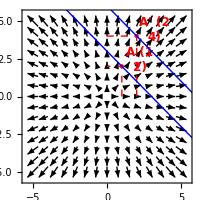

```mathematica
With[{O={0,0},A={1,2},matM=2({{1, 0}, {0, 1}}), xymax=5},
With[{AA=matM.A},
Show[
{
(* Champs de vecteurs *)
VectorPlot[matM.{x, y},
{x, -xymax,xymax},{y, -xymax,xymax}
]/.Hue[0.67,0.6,0.6]->Black,
(* representation du point *)
Graphics[{
PointSize[Large],Red,Point[A],
Text[Style["A (1
2)",Bold,12],A+{1.2,0.4}],
Dashed,Thin,Line[{{A⟦1⟧,0},A,{0,A⟦2⟧}}],
(* Image *)
PointSize[Large],Red,Point[AA],
Text[Style["A' (2
4)",Bold,12],AA+{1.2,0.4}],
Dashed,Thin,Line[{{AA⟦1⟧,0},AA,{0,AA⟦2⟧}}]

}],
(* representation de la droite *)
ParametricPlot[
{
{1+λ, 2-λ}, 
matM.{1+λ, 2-λ}
},
{λ, -xymax,xymax},
PlotStyle->{{Thick,Blue}, Blue}
]
},
ImageSize->200,
Frame->True
]]]
```

On remarque que tous les vecteurs (et les axes passant par (0,0)) sont invariants en direction et en sens.

La droite d’équation paramétrique,  (x
y)=(1+λ
2-λ), où λ∈ℝ, passe par le point A (1
2), est transformée en la droite parallèle d’équation paramétrique,  (x
y)=2(1+λ
2-λ). Le point A (1
2) est transformé en A’ (2
4).

3) 	OverVector[e_1] (1
0) est transformé en  λ OverVector[e_1] (λ
0),	et	OverVector[e_2] (0
1) est transformé en λ OverVector[e_2] =(0
λ)

4)  Matrice : (λ | 0
0 | λ) (1
0)=(λ
0)=λ OverVector[e_1], et 	(λ | 0
0 | λ)(0
1)=(0
λ)=λ OverVector[e_2],  det(λ | 0
0 | λ)=|λ | 0
0 | λ|=λ^2 
La matrice de l’homothétie de rapport λ est λ fois la matrice identité.

#### 2. Symétrie centrale

1) Soit		   f:     ℝ^2⟶ ℝ^2 	avec	 f :(x
y)↦-( x
y) 
2) Champ de vecteurs calculé :

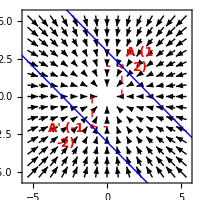

```mathematica
With[{O={0,0},A={1,2},matM=-({{1, 0}, {0, 1}}), xymax=5},
Show[
{
(* Champs de vecteurs *)
VectorPlot[matM.{x, y},
{x, -xymax,xymax},{y, -xymax,xymax}
]/.Hue[0.67,0.6,0.6]->Black,
(* representation du point *)
Graphics[{
PointSize[Large],Red,Point[A],
Text[Style["A (1
2)",Bold,12],A+{1.2,0.4}],
Dashed,Thin,Line[{{A⟦1⟧,0},A,{0,A⟦2⟧}}],
(* Image *)
PointSize[Large],Red,Point[-A],
Text[Style["A' (-1
-2)",Bold,12],-A-{1.8,0.6}],
Dashed,Thin,Line[{-{A⟦1⟧,0},-A,-{0,A⟦2⟧}}]

}],
(* representation de la droite *)
ParametricPlot[
{
{1+λ, 2-λ}, 
matM.{1+λ, 2-λ}
},
{λ, -xymax,xymax},
PlotStyle->{{Thick,Blue}, Blue}
]
},
ImageSize->200,
Frame->True
]]
```

En comparant ce graphe avec le précédent 1. , on observe que chaque vecteur est inversé (retourné de 180°).
Tous les vecteurs sont invariants en direction.

La droite d’équation paramétrique,  (x
y)=(1+λ
2-λ), où λ∈ℝ, passe par le point A (1
2), est transformée en la droite d’équation paramétrique,  (x
y)=-(1+λ
2-λ). A (1
2) est transformé en A’ (-1
-2).

3) OverVector[e_1] (1
0) est transformé en -OverVector[e_1] (-1
0)	et	OverVector[e_2] (0
1) est transformé en -OverVector[e_2] (0
-1)

4) Matrice : (-1 | 0
0 | -1)(1
0)=(-1
0)=-OverVector[e_1], et (-1 | 0
0 | -1)(0
1)=(0
-1)=-OverVector[e_2],  det(-1 | 0
0 | -1)=|-1 | 0
0 | -1|=1

#### 3. Symétrie par rapport à l’axe x

1) Soit		f : ℝ^2 ⟶ ℝ^2 		avec	 f :(x
y)↦( x
-y) 
2) Champ de vecteurs calculé :

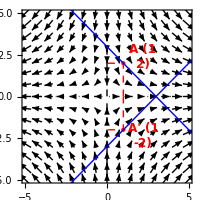

```mathematica
With[{O={0,0},A={1,2}, matM=({{1, 0}, {0, -1}}),xymax=5},
With[{AA=matM.A(*={1,-2}*)},
Show[
{
(* Axes de symétrie : axes x et y *)
{
ParametricPlot[
{
{0,t},
{t,0}
},
{t, -xymax, xymax},
PlotStyle->{{Thick,Dashed,Black},{Thick,Dotted,Black}}
]
},
(* Champs de vecteurs *)
VectorPlot[matM.{x, y},
{x, -xymax,xymax},{y, -xymax,xymax}
]/.Hue[0.67,0.6,0.6]->Black,
(* representation du point *)
Graphics[{
PointSize[Large],Red,Point[A],
Text[Style["A (1
2)",Bold,12],A+{1.2,0.4}],
Dashed,Thin,Line[{{A⟦1⟧,0},A,{0,A⟦2⟧}}],
(* et de son Image *)
PointSize[Large],Red,Point[AA],
Text[Style["A' (1
-2)",Bold,12],matM.(A+{1.2,0.4})],
Dashed,Thin,Line[{{AA⟦1⟧,0},AA,{0,AA⟦2⟧}}]
}],
(* representation de la droite et de sa transformée *)
ParametricPlot[
{
{1+λ, 2-λ}, 
matM.{1+λ, 2-λ}
},
{λ, -xymax,xymax},
PlotStyle->{{Thick,Blue},Blue}
]
},
AspectRatio->1,
ImageSize->200,
Frame->True
]]]
```

On observe directement que les deux axes, tracés en pointillés, sont invariants en direction. Le premier axe (y=0) est aussi invariant en sens (en tirets), tandis que le second (x=0) est inversé en sens (en gros points).

3) 	OverVector[e_1] (1
0) est transformé en OverVector[e_1] (1
0)		et	OverVector[e_2] (0
1) est transformé en  -OverVector[e_2](0
-1)

4)  Matrice : (1 | 0
0 | -1)(1
0)=(1
0)=OverVector[e_1], et 	(1 | 0
0 | -1)(0
1)=(0
-1)=-OverVector[e_2]	det(1 | 0
0 | -1)=|1 | 0
0 | -1|=-1	
5)

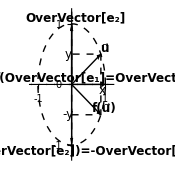

```mathematica
Show[
ParametricPlot[
{
{0,t},
{t,0}
},
{t, -1.2, 1.2},
PlotStyle->{{Thick,Dashed,Black},{Thick,Dotted,Black}},
Ticks->{{-1,0,1},{-1,0,1}}
],
Graphics[{
Thick,
(* Tracé du vecteur Subscript[e, 1] *)
Arrow[{{0,0},{1,0}}],
Arrow[{{0,0},{0,1}}],Text[Style["f(OverVector[e_1]=OverVector[e_1]",Bold,12],{1,0.1}],
(* Tracé du vecteur Subscript[e, 2] et de sa transformation *)
Arrow[{{0,0},{0,1}}],Text[Style["OverVector[e_2]",Bold,12],{0.1,1+0.1}],
Arrow[{{0,0},{0,-1}}],Text[Style["f(OverVector[e_2])=-OverVector[e_2]",Bold,12],{+0.25,-1-0.1}],
(* Tracer cercle en pointillés *)
(* Coordonnées des vecteurs *)
Arrow[{{{0,0},{(√3)/2,1/2}},{{0,0},{(√3)/2,-1/2}}}],
Text[Style["u⃗",Bold,12],{(√3)/2+0.1,1/2+0.1}],
Text[Style["f(u⃗)",Bold,12],{(√3)/2+0.1,-1/2+0.1}],
(* Tracer cercle et coordonnées des vecteurs en pointillés *)
Thin,Dashed,Circle[{0,0},1],
Line[{{0,-1/2},{(√3)/2,-1/2},{(√3)/2,1/2},{0,1/2}}],
Text[Style["x",Thin,12],{(√3)/2+0.05,-0.1}],Text[Style["y",Thin,12],{-0.1,1/2}],
Text[Style["-y",Thin,12],{-0.1,-1/2}]
}],
PlotRange->{{-1.2,1.2},{-1.2,1.2}},
AspectRatio->1,
ImageSize->190
]
```

#### 4. Symétrie par rapport à la première bissectrice

1) Soit		f : ℝ^2 ⟶ ℝ^2 		avec	 f :(x
y)↦( y
x) 
2) Champ de vecteurs calculé :

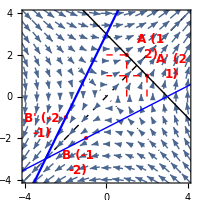

```mathematica
With[{O={0,0},A={1,2}, AA={2,1},matM=({{0, 1}, {1, 0}}),xymax=4},
With[{B=-A, BB=-AA},
Show[
{
(* Axes de symétrie : Premières bissectrices *)
{
Plot[{x,-x},
{x,-xymax, xymax},
PlotStyle->{{Thick,Dashed,Black},{Thick,Dotted,Black}}
]
},
(* Champ de vecteurs *)
VectorPlot[matM.{x,y},
{x,-xymax,xymax},{y,-xymax,xymax}
]/.Hue[0.67,0.6,0.6]->Black,
(* representation du point *)
Graphics[{
PointSize[Large],Red,Point[A],
Text[Style["A (1
2)",Bold,12],A+{1.2,0.4}],
Dashed,Thin,Line[{{A⟦1⟧,0},A,{0,A⟦2⟧}}],
(* Image *)
PointSize[Large],Red,Point[AA],
Text[Style["A' (2
1)",Bold,12],AA+{1.2,0.4}],
Dashed,Thin,Line[{{AA⟦1⟧,0},AA,{0,AA⟦2⟧}}],
(* representation d'un autre point *)
PointSize[Large],Red,Point[B],
Text[Style["B (-1
-2)",Bold,12],B-{0.4,1.2}],
PointSize[Large],Red,Point[BB],
Text[Style["B' (-2
-1)",Bold,12],BB-{1.2,0.4}]
}],
ParametricPlot[
{
(* representation de la droite, qui est invariante ! *)
{1+λ, 2-λ}, 
(* representation d'une autre droite, et de sa droite symétrique *)
{-1+2λ, -2+λ},
matM.{-1+2λ, -2+λ}
},
{λ, -xymax,xymax},
PlotStyle->{{Thick,Black}, {Thick,Blue},Blue}
]
},
AspectRatio->1,
ImageSize->200,
Frame->True
]]]
```

On observe que les deux bissectrices, tracées en pointillés, sont invariantes en direction. La première bissectrice (y=x) est aussi invariante en sens (en tirets), tandis que la seconde bissectrice (y=-x) est inversée en sens (en gros points).

La droite D est perpendiculaire à la première bissectrice (et parallèle à la seconde bissectrice), est globalement invariante par la transformation. Le point A (1
2) est transformé en A’ (2
1).

La droite d’équation paramétrique,  (x
y)=(-1+2λ
-2+λ), où λ∈ℝ, passe par le point B (-1
-2), est transformée en la droite d’équation paramétrique,  (x
y)=(0 | 1
1 | 0)(-1+2λ
-2+λ). B (-1
-2) est transformé en B’ (-2
-1).

3) 	OverVector[e_1] (1
0) est transformé en OverVector[e_2] (0
1), 	et	OverVector[e_2] (0
1) est transformé en OverVector[e_1] (1
0)

4)  Matrice : (0 | 1
1 | 0)(1
0)=(0
1)=OverVector[e_2], 	et 	(0 | 1
1 | 0)(0
1)=(1
0)=OverVector[e_1]	det(0 | 1
1 | 0)=|0 | 1
1 | 0|=-1

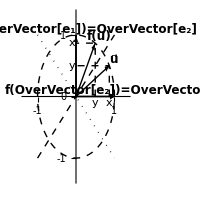

```mathematica
Show[
Plot[{x,-x},
{x, -1, 1},
PlotStyle->{{Thick,Dashed,Black},{Thick,Dotted,Black}},
Ticks->{{-1,0,1},{-1,0,1}}
],
Graphics[{
Thick,
(* Tracé du vecteur Subscript[e, 1] et de sa rotation de 45° *)
Arrow[{{0,0},{1,0}}],
Arrow[{{0,0},{0,1}}],Text[Style["f(OverVector[e_1])=OverVector[e_2]",Bold,12],{+0.2,1+0.1}],
(* Tracé du vecteur Subscript[e, 2] et de sa rotation de 45° *)
Arrow[{{0,0},{0,1}}],
Arrow[{{0,0},{1,0}}],Text[Style["f(OverVector[e_2])=OverVector[e_1]",Bold,12],{1+0.1,+0.1}],
(* Tracer cercle en pointillés *)
(* Coordonnées des vecteurs *)
Arrow[{{{0,0},{(√3)/2,1/2}},{{0,0},{1/2,(√3)/2}}}],
Text[Style["u⃗",Bold,12],{(√3)/2+0.1,1/2+0.1}],
Text[Style["f(u⃗)",Bold,12],{1/2+0.1,(√3)/2+0.1}],
(* Tracer cercle et coordonnées des vecteurs en pointillés *)
Thin,Dashed,Circle[{0,0},1],
Line[{{{(√3)/2,0},{(√3)/2,1/2},{0,1/2}},{{1/2,0},{1/2,(√3)/2},{0,(√3)/2}}}],
Text[Style["x",Thin],{(√3)/2,-0.1}],Text[Style["y",Thin],{-0.1,1/2}],
Text[Style["y",Thin],{1/2,-0.1}],Text[Style["x",Thin],{-0.1,(√3)/2}]
}],
PlotRange->{{-1.35,1.35},{-1.35,1.35}},
AspectRatio->1,
ImageSize->200
]
```

#### 5. Rotation d’angle θ=45°

1) Soit		f : ℝ^2 ⟶ ℝ^2 	avec	 f :(x
y)↦( x/(√2)-y/(√2)
 x/(√2)+y/(√2))=(Cos[θ] x-Sin[θ]y
Cos[θ]  x+Sin[θ]y) où θ=π/4 
2) Champ de vecteurs calculé :

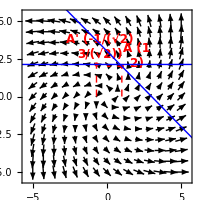

```mathematica
(* 
({{1/(√2), -1/(√2)}, {1/(√2), 1/(√2)}}).({{1+λ}, {2-λ}})==({{(λ+1)/(√2)-(2-λ)/(√2)}, {(2-λ)/(√2)+(λ+1)/(√2)}})==({{(2 λ-1)/(√2)}, {3/(√2)}})//Simplify;

({{1/(√2), -1/(√2)}, {1/(√2), 1/(√2)}}).({{1}, {2}})==({{1/(√2)-√2}, {1/(√2)+√2}})==({{-1/(√2)}, {3/(√2)}})//Simplify//TraditionalForm
*)
With[{matM=({{1/(√2), -1/(√2)}, {1/(√2), 1/(√2)}}),O={0,0},A={1,2},xymax=5},
With[{ AA=matM.A},
Show[
{
(* Axes de symétrie : Il n'y en a pas ! *)
(*{
ParametricPlot[
{
{0,t},
{t,0}
},
{t, -xymax, xymax},
PlotStyle->{{Thick,Dashed,Black},{Thick,Dotted,Black}}
]
},*)
(* Champs de vecteurs *)
VectorPlot[matM.{x, y},
{x, -xymax,xymax},{y, -xymax,xymax}
]/.Hue[0.67,0.6,0.6]->Black,
(* representation du point *)
Graphics[{
PointSize[Large],Red,Point[A],
Text[Style["A (1
2)",Bold,12],A+{1.,0.7}],
Dashed,Thin,Line[{{A⟦1⟧,0},A,{0,A⟦2⟧}}],
(* Image *)
PointSize[Large],Red,Point[AA],
Text[Style["A' (-1/(√2)
3/(√2))",Bold,12],matM.(A+{1.,0.7})],
Dashed,Thin,Line[{{AA⟦1⟧,0},AA,{0,AA⟦2⟧}}]
}],
(* representation de la droite et de sa transformée *)
ParametricPlot[
{{1+λ, 2-λ}, 
matM.{1+λ, 2-λ}
},
{λ, -xymax,xymax},
PlotStyle->{{Thick,Blue},Blue}
]
},
AspectRatio->1,
ImageSize->200,
Frame->True
]]]
```

On n’observe pas de directions invariantes (réelles) : tous les vecteurs sont tournés de 45°.

La droite d’équation paramétrique,  (x
y)=(1+λ
2-λ) , où λ∈ℝ, qui passe par le point A (1
2) est transformée en la droite d’équation paramétrique,  (x
y)=1/(√2)(1 | -1
1 | 1) (1+λ
2-λ)=1/(√2)(1+λ-(2-λ)
1+λ+(2-λ))=1/(√2)(2 λ-1
3).
Le point A (1
2) est transformé en A’ 1/(√2)(1-2
1+2)=1/(√2)(-1
3).

3) 	OverVector[e_1] (1
0) est transformé en f(OverVector[e_1])=1/(√2)(1
1) 	et	OverVector[e_2] (0
1) est transformé en f (OverVector[e_2])= 1/(√2)(-1
1)

4) On construit la matrice R(45°)=1/(√2)(1 | -1
1 | 1) à partir du tableau des images, on retrouve 
1/(√2)(1 | -1
1 | 1) (1
0)=(1/(√2)
1/(√2)) =R(45°)OverVector[e_1], et	1/(√2)(1 | -1
1 | 1) (0
1)=(1/(√2)
1/(√2)) =R(45°) OverVector[e_2], det(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))=1
5)

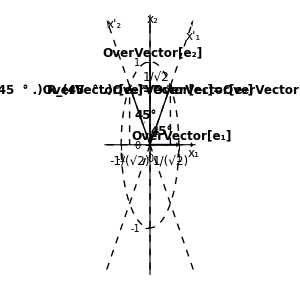

```mathematica
Show[
Plot[0,{x, 0,1},Ticks->{{-1,0,1},{-1,0,1}}],
Graphics[{
Thick,
(* Tracé du vecteur Subscript[e, 1] et de sa rotation de 45° *)
Arrow[{{0,0},{1,0}}],Text[Style["OverVector[e_1]",Bold,12],{1+0.1,0.1}],
Arrow[{{0,0},{1/(√2),1/(√2)}}],Text[Style["R_(45  ° .)OverVector[e_1]=OverVector[e_1]",Bold,12],{1/(√2)+0.5,1/(√2)-0.05}],
(* Tracé du vecteur Subscript[e, 2] et de sa rotation de 45° *)
Arrow[{{0,0},{0,1}}],Text[Style["OverVector[e_2]",Bold,12],{+0.1,1+0.1}],
Arrow[{{0,0},{-1/(√2),1/(√2)}}],Text[Style["R_(45  ° .)OverVector[e_2]=OverVector[e_2]",Bold,12],{-1/(√2)-0.5,1/(√2)-0.05}],
Dotted,Circle[{0,0},1/3, {0,π/4}],Text[Style["45°",Bold,12],{+0.4,0.16}],
Dotted,Circle[{0,0},1/3, {π/2,3π/4}],Text[Style["45°",Bold,12],{-0.16,0.35}],
(* Tracer cercle en pointillés *)
Thin,Dashed,Circle[{0,0},1],
(* Tracer des anciens axes *)
Arrow[{{{-1.5,0},{1.5,0}}, {{0,-1.5},{0,1.5}}}],
Text[Style["x_1",Thin,12],{1.5,-0.1}],
Text[Style["x_2",Thin,12],{+0.1,1.5}],
(* Tracer des nouveaux axes *)
Arrow[{{{-1.5,-1.5},{1.5,1.5}}, {{1.5,-1.5},{-1.5,1.5}}}],
Text[Style["x'_1",Thin,12],{1.5,1.5-0.2}],
Text[Style["x'_2",Thin,12],{-1.5+0.25,1.5-0.05}],
(* Coordonnées des vecteurs *)
Line[{{1/(√2),0},{1/(√2),1/(√2)},{-1/(√2),1/(√2)},{-1/(√2),0}}],
Text[Style["1/(√2)",Thin, 12],{1/(√2),-0.2}],
Text[Style["1/√2",Thin,12],{+0.2,1/(√2)+0.1}],
Text[Style["-1/(√2)",Thin,12],{-1/(√2),-0.2}]
}],
PlotRange->All,
AspectRatio->1,
ImageSize->300
]
```

#### 6. Projection sur v⃗ ( α β)=( 2 1)

1) Soit		f : ℝ^2 ⟶ ℝ^2 	avec	 f :(x
y)↦1/5(4 | 2
2 | 1)(x
y) 	
2) Champ de vecteurs calculé pour :

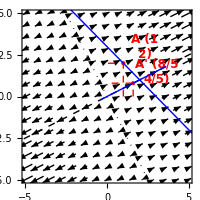

```mathematica
(*(({{Cos[θ]^2, Sin[θ]Cos[θ]}, {Sin[θ]Cos[θ], Sin[θ]^2}})/.θ->ArcCos[2/(√5)]).{1,2}=={8/5,4/5}*)
With[{θ=ArcCos[2/(√5)]},
With[{O={0,0},A={1,2},
matM=({{Cos[θ]^2, Sin[θ]Cos[θ]}, {Sin[θ]Cos[θ], Sin[θ]^2}}),xymax=5},
With[{ AA=matM.A},
Show[
{
ParametricPlot[
{
{2t,t},
{-t/2,t}
},
{t, -xymax, xymax},
PlotStyle->{{Thick,Dashed,Black},{Thick,Dotted,Black}}
],
VectorPlot[matM.{x, y},
{x, -xymax, xymax},{y, -xymax, xymax}
]/.Hue[0.67,0.6,0.6]->Black,
(* representation du point *)
Graphics[{
PointSize[Large],Red,Point[A],
Text[Style["A (1
2)",Bold,12],A+{1.3,1.0}],
Dashed,Thin,Line[{{A⟦1⟧,0},A,{0,A⟦2⟧}}],
(* et de son Image *)
PointSize[Large],Red,Point[AA],
Text[Style["A' (8/5
4/5)",Bold,12],matM.(A+{1.3,1.0})],
Dashed,Thin,Line[{{AA⟦1⟧,0},AA,{0,AA⟦2⟧}}]
}],
(* representation de la droite et de sa transformée *)
ParametricPlot[
{
{1+λ, 2-λ}, 
matM.{1+λ, 2-λ}
},
{λ, -xymax,xymax},
PlotStyle->{{Thick,Blue},{Thick,Blue}}
]
},
PlotRange->{{-xymax, xymax},{-xymax, xymax}},
AspectRatio->1,
ImageSize->200,
Frame->True
]]]]
```

On observe qu’il n’y a qu’un seul axe invariant (y=2x), et que l’image de l’axe perpendiculaire est le seul vecteur (x=y=0) figuré par le point (x=y=0).

La droite d’équation paramétrique,  (x
y)=(1+λ
2-λ) , où λ∈ℝ, qui passe par le point A (1
2) est transformée en la droite d’équation paramétrique,  (x
y)=1/5(4 | 2
2 | 1) (1+λ
2-λ)=1/5(4 (λ+1)+2 (2-λ)
2 (λ+1)+2-λ)=1/5(2 (λ+4)
λ+4), i.e. d’équation cartésienne (y=2x) : c’est l’équation de l’axe invariant. En fait on peut montrer que l’image de toute droite du plan est l’axe invariant : c’est une projection sur cette droite.
Le point A (1
2) est transformé en A’ 1/5(4 | 2
2 | 1) (1
2)=1/5(8
4).

3) 2 OverVector[e_1]+OverVector[e_2]  (2
1) est transformé en (2
1), et	OverVector[e_1]-2 OverVector[e_2] (1
-2) est transformé en (0
0)

4)  Matrice : 1/5(4 | 2
2 | 1) (1
0)=1/5(4
2), et 	1/5(4 | 2
2 | 1) (0
1)=1/5(2
1),	det(4/5 | 2/5
2/5 | 1/5)=|4/5 | 2/5
2/5 | 1/5|=0
5)

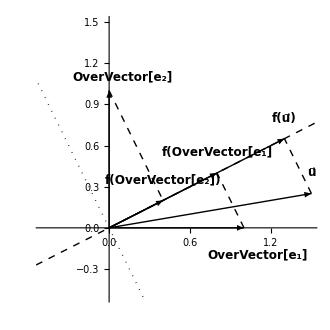

```mathematica
Show[
ParametricPlot[
{
{2t,t},
{-t/2,t}
},
{t, -10, 10},
PlotStyle->{{Thick,Dashed,Black},{Thick,Dotted,Black}}
],
With[{e1={1,0},e2={0,1},O={0,0},U={3/2,1/4},
θ=ArcCos[2/(√5)],D={0,+0.15}},
With[{M=({{Cos[θ]^2, Sin[θ]Cos[θ]}, {Sin[θ]Cos[θ], Sin[θ]^2}})},
Graphics[{
Thick,
(* Tracé du vecteur Subscript[e, 1] et de sa transformation*)
Arrow[{O,e1}],Text[Style["OverVector[e_1]",Bold,12],e1+{.1,-0.2}],
Arrow[{O,M.e1}],
Text[Style["f(OverVector[e_1]",Bold,12],M.e1+D],
(* Tracé du vecteur Subscript[e, 2] et de sa transformation *)
Arrow[{{0,0},{0,1}}],Text[Style["OverVector[e_2]",Bold,12],e2+{0.1,0.1}],
Arrow[{{0,0},M.{0,1}}],Text[Style["f(OverVector[e_2])",Bold,12],M.e2+D],
(* Tracer cercle en pointillés *)
(* Coordonnées des vecteurs *)
Arrow[{{O,U},{O,M.U}}],
Text[Style["u⃗",Bold,12],U+D],
Text[Style["f(u⃗)",Bold,12],M.U+D],
(* Tracer cercle et coordonnées des vecteurs en pointillés *)
(*Thin,Dashed,Circle[{0,0},1],*)
Thin,Dashed,Line[{{e1,M.e1},{e2,M.e2},{U,M.U}}]
(**)
}]]],
PlotRange->{{-0.5,1.5},{-0.5,1.5}},
AspectRatio->2/2,
ImageSize->330
]
```

#### 7. Symétrie orthogonale par rapport à v⃗ ( α β)=( 2 1)

1) Soit		f : ℝ^2 ⟶ ℝ^2 	avec	 f :(x
y)↦1/5(3 | 4
4 | -3)(x
y) 	
2) Champ de vecteurs calculé pour :

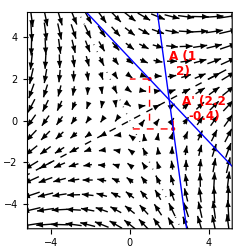

```mathematica
(*(({{Cos[2θ], Sin[2θ]}, {Sin[2θ], -Cos[2θ]}})/.θ->ArcCos[2/(√5)]).{1,2}=={2.2,-0.4}*)
With[{θ=ArcCos[2/(√5)]},
With[{O={0,0},A={1,2},
matM=({{Cos[2θ], Sin[2θ]}, {Sin[2θ], -Cos[2θ]}}),xymax=5},
With[{ AA=matM.A},
Show[
{
ParametricPlot[
{
{2t,t},
{-t/2,t}
},
{t, -xymax, xymax},
PlotStyle->{{Thick,Dashed,Black},{Thick,Dotted,Black}}
],
VectorPlot[matM.{x, y},
{x, -xymax, xymax},{y, -xymax, xymax}
]/.Hue[0.67,0.6,0.6]->Black,
(* representation du point *)
Graphics[{
PointSize[Large],Red,Point[A],
Text[Style["A (1
2)",Bold,12],A+{1.7,0.7}],
Dashed,Thin,Line[{{A⟦1⟧,0},A,{0,A⟦2⟧}}],
(* et de son Image *)
PointSize[Large],Red,Point[AA],
Text[Style["A' (2.2
-0.4)",Bold,12],matM.(A+{1.7,0.7})],
Dashed,Thin,Line[{{AA⟦1⟧,0},AA,{0,AA⟦2⟧}}]
}],
(* representation de la droite et de sa transformée *)
ParametricPlot[
{
{1+λ, 2-λ}, 
matM.{1+λ, 2-λ}
},
{λ, -xymax,xymax},
PlotStyle->{{Thick,Blue},{Blue}}
]
},
PlotRange->{{-xymax, xymax},{-xymax, xymax}},
AspectRatio->1,
ImageSize->250,
Frame->True
]]]]
```

On observe que les deux axes, tracés en pointillés, sont invariants en direction. Le premier axe (y=2x) est aussi invariant en sens (en tirets), tandis que le second ((y=-x/2) est inversé en sens (en gros points).

La droite d’équation paramétrique,  (x
y)=(1+λ
2-λ) , où λ∈ℝ, qui passe par le point A (1
2) est transformée en la droite d’équation paramétrique,  (x
y)=1/5(3 | 4
4 | -3) (1+λ
2-λ)=(2.2-0.2 λ
1.4 λ-0.4) et A (1
2) en A’ (2.2
-0.4).

3) 2 OverVector[e_1]+OverVector[e_2]  (2
1) est transformé en 1/5(3 | 4
4 | -3) (2
1)=(2
1), et OverVector[e_1]-2 OverVector[e_2] (1
-2) en 1/5(3 | 4
4 | -3)(1
-2)=-(1
-2)

4)  Matrice : 1/5(3 | 4
4 | -3) (1
0)=1/5(3
4), et 1/5(3 | 4
4 | -3) (0
1)=1/5(4
-3), det(3/5 | 4/5
4/5 | -3/5)=|3/5 | 4/5
4/5 | -3/5|=-1
5)

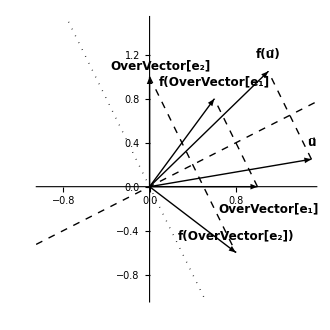

```mathematica
Show[
ParametricPlot[
{
{2t,t},
{-t/2,t}
},
{t, -10, 10},
PlotStyle->{{Thick,Dashed,Black},{Thick,Dotted,Black}}
],
With[{e1={1,0},e2={0,1},O={0,0},U={3/2,1/4},
θ=ArcCos[2/(√5)],D={0,+0.15}},
With[{M=({{Cos[2θ], Sin[2θ]}, {Sin[2θ], -Cos[2θ]}})},
Graphics[{
Thick,
(* Tracé du vecteur Subscript[e, 1] et de sa transformation*)
Arrow[{O,e1}],Text[Style["OverVector[e_1]",Bold,12],e1+{.1,-0.2}],
Arrow[{O,M.e1}],
Text[Style["f(OverVector[e_1]",Bold,12],M.e1+D],
(* Tracé du vecteur Subscript[e, 2] et de sa transformation *)
Arrow[{{0,0},{0,1}}],Text[Style["OverVector[e_2]",Bold,12],e2+{0.1,0.1}],
Arrow[{{0,0},M.{0,1}}],Text[Style["f(OverVector[e_2])",Bold,12],M.e2+D],
(* Tracer cercle en pointillés *)
(* Coordonnées des vecteurs *)
Arrow[{{O,U},{O,M.U}}],
Text[Style["u⃗",Bold,12],U+D],
Text[Style["f(u⃗)",Bold,12],M.U+D],
(* Tracer cercle et coordonnées des vecteurs en pointillés *)
(*Thin,Dashed,Circle[{0,0},1],*)
Thin,Dashed,Line[{{e1,M.e1},{e2,M.e2},{U,M.U}}]
(**)
}]]],
PlotRange->{{-1,1.5},{-1,1.5}},
AspectRatio->2/2,
ImageSize->330
]
```

#### 8. Cisaillement le long de x

1) Soit		f : ℝ^2 ⟶ ℝ^2 avec	 f :(x
y)↦(1 | 0.8
0 | 1)(x
y) 	
Le cisaillement est d’autant plus fort que l’on s’éloigne de l’axe x.
2) Champ de vecteurs calculé :

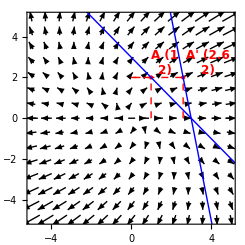

```mathematica
(*({{1, 0.8}, {0, 1}}).{1,2}=={2.6,2.}*)
With[{O={0,0},A={1,2},
matM=({{1, 0.8}, {0, 1}}),xymax=5},
With[{ AA=matM.A},
Show[
{
ParametricPlot[
{
{t,0}
},
{t, -xymax, 10},
PlotStyle->{{Thick,Dashed,Black},{Thick,Dotted,Black}}
],

VectorPlot[matM.{x, y},
{x, -xymax, xymax},{y, -xymax, xymax}
]/.Hue[0.67,0.6,0.6]->Black,
(* representation du point *)
Graphics[{
PointSize[Large],Red,Point[A],
Text[Style["A (1
2)",Bold,12],A+{0.7,0.7}],
Dashed,Thin,Line[{{A⟦1⟧,0},A,{0,A⟦2⟧}}],
(* et de son Image *)
PointSize[Large],Red,Point[AA],
Text[Style["A' (2.6
2)",Bold,12],matM.(A+{0.7,0.7})],
Dashed,Thin,Line[{{AA⟦1⟧,0},AA,{0,AA⟦2⟧}}]
}],
(* representation de la droite et de sa transformée *)
ParametricPlot[
{
{1+λ, 2-λ}, 
matM.{1+λ, 2-λ}
},
{λ, -xymax,10},
PlotStyle->{{Thick,Blue},{Blue}}
]
},
PlotRange->{{-xymax, xymax},{-xymax, xymax}},
AspectRatio->1,
ImageSize->245,
Frame->True
]]]
```

On observe directement qu’il n’y a qu’un seul axe invariant (y=0) en direction, et en sens (en tirets).

La droite d’équation paramétrique,  (x
y)=(1+λ
2-λ) , où λ∈ℝ, qui passe par le point A (1
2) est transformée en la droite d’équation paramétrique,  (x
y)=(1 | 0.8
0 | 1) (1+λ
2-λ)=(0.2 λ+2.6
2-λ).

3) OverVector[e_1]  (1
0) est transformé en OverVector[e_1] (1
0), et	OverVector[e_2] (0
1) est transformé en 0.8 OverVector[e_1] +OverVector[e_2]  (0.8
1)

4)  Matrice : (1 | 0.8
0 | 1) (1
0)=(1
0), et 	(1 | 0.8
0 | 1) (0
1)=(0.8
1), 	det(1 | 0.8
0 | 1)=|1 | 0.8
0 | 1|=1
5)

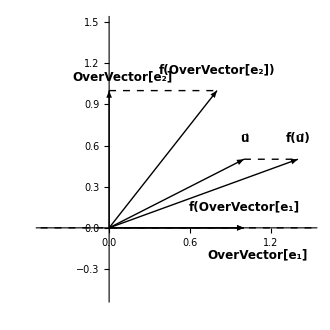

```mathematica
Show[
ParametricPlot[
{
{t,0}
},
{t, -10, 10},
PlotStyle->{{Thick,Dashed,Black},{Thick,Dotted,Black}}
],
With[{e1={1,0},e2={0,1},O={0,0},U={1,1/2},
θ=ArcCos[2/(√5)],D={0,+0.15}},
With[{M=({{1, 0.8}, {0, 1}})},
Graphics[{
Thick,
(* Tracé du vecteur Subscript[e, 1] et de sa transformation*)
Arrow[{O,e1}],Text[Style["OverVector[e_1]",Bold,12],e1+{.1,-0.2}],
Arrow[{O,M.e1}],
Text[Style["f(OverVector[e_1]",Bold,12],M.e1+D],
(* Tracé du vecteur Subscript[e, 2] et de sa transformation *)
Arrow[{{0,0},{0,1}}],Text[Style["OverVector[e_2]",Bold,12],e2+{0.1,0.1}],
Arrow[{{0,0},M.{0,1}}],Text[Style["f(OverVector[e_2])",Bold,12],M.e2+D],
(* Tracer cercle en pointillés *)
(* Coordonnées des vecteurs *)
Arrow[{{O,U},{O,M.U}}],
Text[Style["u⃗",Bold,12],U+D],
Text[Style["f(u⃗)",Bold,12],M.U+D],
(* Tracer cercle et coordonnées des vecteurs en pointillés *)
(*Thin,Dashed,Circle[{0,0},1],*)
Thin,Dashed,Line[{{e1,M.e1},{e2,M.e2},{U,M.U}}]
(**)
}]]],
PlotRange->{{-0.5,1.5},{-0.5,1.5}},
AspectRatio->2/2,
ImageSize->330
]
```

## II. Bibliographie

### A. Références disponibles sur MOODLE 4M062

#### 1. Livres et Articles

https://www.wolfram.com/language/elementary-introduction/
EIWLStephenWolfram-ElementaryIntroductionWolframLanguage(2015).pdf

un-langage-pour-ingenieurThierryVerdel2012.pdf

Strogatz-Nonlinear Dynamics and Chaos-00---1994.pdf

RomeoJulietSprottNLDPLS2004.pdf

### B. Originaux des 2 Wolfram Demonstrations utilisées

#### PhasePortraitAndFieldDirectionsOfTwoDimensionalLinearSystems

```mathematica
Manipulate[
m={{a1,b1},{a2,b2}};
Show[
VectorPlot[
m.{x,y},{x,-10,10},{y,-10,10},
StreamPoints->{{pt1,pt2,pt3,pt4}},
StreamStyle->{Red,Thick},ImageSize->{460,310}
],
Graphics[{
Thick,Orange,
Map[
Line[{-100#,100#}]&,
Select[Eigenvectors[m],(Im[#[[1]]]==0&&Im[#[[2]]]==0)&]
]
}],
PlotLabel->Row[{
Column[
{Row[{Column[{Style["ẋ",Italic],Style["ẏ",Italic]}],Column[{" = "," = "}],TableForm[m.{Style["x",Italic],Style["y",Italic]}]//N}]}],
"  ",
Column[{"Eigenvalues:",NumberForm[Chop@N@Eigenvalues[m],{4,2}]}],
"  ",,
Column[{"Eigenvectors:",NumberForm[Chop@N@Eigenvectors[m][[1]],{4,2}],NumberForm[Chop@N@Eigenvectors[m][[2]],{4,2}] }]
}]
],
Style["ẋ= a_1x + b_1y",Bold],
{{a1,1,"a_1"},-10,10,Appearance->"Labeled"},
{{b1,1,"b_1"},-10,10,Appearance->"Labeled"},
Style["ẏ = a_2x + b_2y",Bold],
{{a2,2,"a_2"},-10,10,Appearance->"Labeled"},{{b2,-2,"b_2"},-10,10,Appearance->"Labeled"},{{pt1,{-5.1,4.8}},{-10,-10},{10,10},Locator},
{{pt2,{4.9,5.1}},{-10,-10},{10,10},Locator},
{{pt3,{-4.9,-5}},{-10,-10},{10,10},Locator},
{{pt4,{4.9,-5.2}},{-10,-10},{10,10},Locator},
TrackedSymbols->True
]
```

#### HomogeneousLinearSystemOfCoupledDifferentialEquations

```mathematica
(*Original*)
Manipulate[
With[{dvec=({{x'}, {y'}}),vec=({{x}, {y}}),mat=({{a, b}, {c, d}})},
With[{esys=Eigensystem[{{a,b},{c,d}}]},
With[{λ1=esys⟦1,1⟧,λ2=esys⟦1,2⟧,
vec1=({{esys⟦2,1⟧⟦1⟧}, {esys⟦2,1⟧⟦2⟧}}),
vec2=({{esys⟦2,2⟧⟦1⟧}, {esys⟦2,2⟧⟦2⟧}})
},
With[{
sol=Text@TraditionalForm@Row[{dvec , " = " , mat, vec}],
eval1=Text@TraditionalForm@Row[{"λ_1 = ",NumberForm[λ1,{5,2}]}],
eval2=Text@TraditionalForm@Row[{"λ_2 = ",NumberForm[λ2,{5,2}]}],
evec1=Text@TraditionalForm@Row[{"ν_1 = ",NumberForm[vec1,{5,2}]}],
evec2=Text@TraditionalForm@Row[{"ν_2 = ",NumberForm[vec2,{5,2}]}]
},
Grid[{{
Style[Text@Column[{
sol,
"",
eval1,
eval2,
"",
evec1,
evec2,
"                                                      ",
}],12],
VectorPlot[
{a*x+b*y,c*x+d*y},{x,-1,1},{y,-1,1},
StreamPoints->{{p[[1]],p[[2]]}},StreamStyle->{Red,Thick},VectorScale->{Tiny,Automatic,None},
Epilog->{Point[p]},ImageSize->{400,400},FrameLabel->{x,y}
]
}}
]]]]],
Style["matrix entries",Bold],
Row[{
Control[{{a,.5,"a"},-1,1,.01,Appearance->"Labeled"}],
Control[{{b,-.75,"b"},-1,1,.01,Appearance->"Labeled"}]
}],
Row[{
Control[{{c,.1,"c"},-1,1,.01,Appearance->"Labeled"}],
Control[{{d,.5,"d"},-1,1,.01,Appearance->"Labeled"}]
}],
{{p,{.5,.5}},{-1,-1},{1,1},Locator},
{sol,ControlType->None},
{eval1,ControlType->None},
{eval2,ControlType->None},
{evec1,ControlType->None},
{evec2,ControlType->None},
TrackedSymbols:>{a,b,c,d,p},
AutorunSequencing->{1,2,3,4,5}
]
```

## III. Wolfram Demonstrations

Cf. http://demonstrations.wolfram.com

Listes non exhaustives classées de Wolfram Demonstrations d’intérêt pour l’UE 4M062, disponibles sur MOODLE.

### A. Les Classiques Indispensables

#### 1BifurcationsCanoniquesLocales

BifurcationDiagramsWithFlowFields-author.nb
BifurcationsInFirstOrderODEs-author.nb
EffectOfAPerturbationOnTheStablePointsOfADynamicalSystem-author.nb

#### 2ProiesPredateurs

AModelForPopulationGrowth-author.nb
PredatorPreyModel-author.nb
PredatorPreyEquations-author.nb

#### 3ODE_Lineaires

CauchysProblem-author.nb
FixedPointOfA2x2LinearSystemOfODEs-author.nb
HomogeneousLinearSystemOfCoupledDifferentialEquations-author.nb
LinearFirstOrderDifferentialEquation-author.nb
PhasePortraitAndFieldDirectionsOfTwoDimensionalLinearSystems-author.nb
RomeoAndJuliet-author.nb
UsingEigenvaluesToSolveAFirstOrderSystemOfTwoCoupledDifferen-author.nb
VisualizingTheSolutionOfTwoLinearDifferentialEquations-author.nb

#### 4IntegrationNumerique

EulersMethodForTheExponentialFunction-author.nb

#### 5Attracteurs

LorenzAttractor-author.nb
TheRosslerAttractor-author.nb

#### 5Lyapunov

AsymptoticStabilityOfDynamicalSystemByLyapunovsDirectMethod-author.nb
FiniteLyapunovExponentForGeneralizedLogisticMapsWithZUnimoda-author.nb
LyapunovExponentsForTheLogisticMap-author.nb

#### 5SensibiliteAuxConditionsInitiales

SensitiveDependenceInIteratedMaps-author.nb
SensitiveDependenceOnInitialConditionsInASimpleThreeBodyProb-author.nb
SensitivityToInitialConditionsInChaos-author.nb

### B. Suppléments

#### 1Bifurcations

BifurcationDiagramForAGeneralizedLogisticMap-author.nb
BifurcationDiagramsWithFlowFields-author.nb
FeigenbaumsScalingRelationForSuperstableParameterValuesBifur-author.nb
HopfBifurcationInTheSelkovModel-author.nb
StructuralInstabilityOfASupercriticalPitchforkBifurcation-author.nb
TypicalBifurcationsOfWavefrontIntersections-author.nb
TypicalBifurcationsOfWavefrontsIn2DAnd3D-author.nb

#### 2ProiesPredateurs

ATriangleModelOfCriminality-author.nb
BifurcationInAModelOfSpruceBudwormPopulations-author.nb
BudwormPopulationDynamics-author.nb
ChaosInTumorGrowthModelWithTimeDelayedImmuneResponse-author.nb
EcologyOfReefSystems-author.nb
EcosystemDynamics-author.nb
FoodWebs.cdf
PopulationSizesAndInteractionsDuringTheZombieApocalypse-author.nb
PredatorPreyDynamicsWithTypeTwoFunctionalResponse-author.nb
PredatorPreyEcosystemARealTimeAgentBasedSimulation-author.nb
PredatorPreyEquationsSimulatingAnImmuneResponse-author.nb
PursuitCurves-author.nb
ShellParameterSpace-author.nb
SynchronizationOfChaoticAttractors-author.nb

#### 3ODE_NonLineaires

3DVectorFields-author.nb
FamiliesOfSolutionsForODEs-author.nb
PhasePlanePlotOfTheVanDerPolDifferentialEquation-author.nb
TheMurderMysteryMethodForIdentifyingAndSolvingExactDifferent-author.nb

#### 4IntegrationNumerique

ASolutionOfEulersTypeForAnExactDifferentialEquation-author.nb
ComparingLeapfrogMethodsWithOtherNumericalMethodsForDifferen-author.nb
DifferenceEquationVersusDifferentialEquation-author.nb
GlobalAndLocalErrorsInRungeKuttaMethods-author.nb
NumericalMethodsForDifferentialEquations-author.nb
PicardsMethodForOrdinaryDifferentialEquations-author.nb
UnderstandingRungeKutta-author.nb

-Graphics-